# Understanding arXiv:2109.10373v2 [hep-ph]

## Trying to understand and replicate the work in Higher-Order Kinematical Effects in Deeply Virtual Compton Scattering. Written by Dima Watkins [bem8mq@virginia.edu]

## (#0): Mathematica Meta:

```mathematica
$ProcessorCount
$MachinePrecision
```

14

15.9546

## (#1): Packages:

## (#1.1): FeynCalc:

```mathematica
<<FeynCalc`
```

FeynCalc is already loaded! If you are trying to reload FeynCalc or load FeynArts, TARCER, PHI, FeynHelpers or any other add-on, please restart the kernel.

$Aborted

## (#2): Good Mathematica Practice:

```mathematica
ClearAll["Global`*"];
ClearScalarProducts;
```

## (#3): Substitutions:

## (#3.1): Kinematics:

### (#3.1.1): Kinematics Point 1 | “The Standard JLab One”

```mathematica
kinematicSetting1={
y->0.49624,
M->0.938,
Q->Sqrt[1.82],
t->-0.17,
xB->0.34,
Subscript[α, EM]->1/137.036,
ℋ->-0.897+I 2.421,
ℋT->2.444+I 1.131,
ℰ->-0.541+I 0.903,
ℰT->2.207+I 5.383
};
```

### (#3.1.2): Kinematics Point 2 | Future Kinematics

```mathematica
kinematicSetting2={
y->0.61881,
M->0.938,
Q->Sqrt[4.55],
t->-0.26,
xB->0.37,
Subscript[α, EM]->1/137.036,
ℋ->-0.884+I 1.851,
ℋT->3.118+I 0.911,
ℰ->-0.424+I 0.649,
ℰT->2.900+I 3.915};
```

## (#3.2): Lightcone Choice:

### (#3.2.1): Lightcone Choice | BKM:

```mathematica
lightconeBKMSetting={αParameter->1/2,βParameter->1/2};
```

### (#3.2.2): Lightcone Choice | UVA:

```mathematica
lightconeUVASetting={αParameter->1,βParameter->1};
```

### (#3.2.3): Lightcone Choice | Ji:

```mathematica
lightconeJiSetting={αParameter->1,βParameter->1/2};
```

### (#3.2.4): Lightcone Choice | BMP:

```mathematica
lightconeBMPSetting={αParameter->0,βParameter->10000};
```

## (#3.3): Other Substitutions:

### (#3.3.1): Others | Skewness ξ

This substitution for ξ comes from Equation (3.10) in the paper.

```mathematica
ξsub={ξ->xB/(2-xB)-(2 xB (2 M^2 xB^2 αParameter+t (-1+xB) (1-2 αParameter+xB (-1+βParameter))))/((-2+xB)^2 (1+xB (-1+βParameter))Q^2)};
```

## (#4): FeynCalc Computations:

## (#4.1): Compton Tensor:

What is written below seems to be: (√2 ϵ_abcd q^c q'^d)/(-√(ϵ_abcd q^c q'^d ϵ^abcd q_c q'_d))

```mathematica
ϵt[a_,b_]:=(Sqrt[2]*Eps[LorentzIndex[a],LorentzIndex[b],Momentum[q],Momentum[qp]])/(-Sqrt[Contract[Eps[LorentzIndex[a],LorentzIndex[b],Momentum[q],Momentum[qp]]*Eps[LorentzIndex[a],LorentzIndex[b],Momentum[q],Momentum[qp]]]]);

gt[a_,b_]:=Contract[ϵt[a,c]*ϵt[b,c]];

𝒯1[a_,b_]:=-1/2 gt[a,b];

𝒯1t[a_,b_]:=ⅈ/2 ϵt[a,b];
```

## (#4.2): Target Polarization Vector:

### (#4.2.1): First Equation of (3.24):

```mathematica
SL[μ_]:=M/(1+ξ)(-FV[n,μ]+SP[n,p]/M^2 FV[p,μ]);
```

### (#4.2.2): Second Equation of (3.24):

```mathematica
STin[μ_]:=1/((1+ξ)Sqrt[-4M^2ξ^2-t(1-ξ^2)])(Contract[Eps[LorentzIndex[μ],LorentzIndex[ν],Momentum[p],Momentum[n]]*Eps[Momentum[n],Momentum[p],Momentum[pp],LorentzIndex[ν]]]);
```

### (#4.2.3): Third Equation of (3.24):

```mathematica
STout[μ_]:=1/Sqrt[-4M^2ξ^2-t(1-ξ^2)] Eps[Momentum[n],Momentum[p],Momentum[pp],LorentzIndex[μ]];
```

## (#4.3): Leptonic Tensor:

### (#4.3.1): Leptonic Tensor | DVCS | Unpolarized Target

```mathematica
LDVCSunp=Simplify[DiracSimplify[1/2*FermionSpinSum[ComplexConjugate[SpinorUBar[kp].(GA[α1]/Q^2).SpinorU[k]]*SpinorUBar[kp].(GA[α2]/Q^2).SpinorU[k]]],{h^2==1}];
```

### (#4.3.2): Leptonic Tensor | DVCS | Polarized Target

```mathematica
LDVCSp=Simplify[-ⅈ*DiracSimplify[1/2*FermionSpinSum[ComplexConjugate[SpinorUBar[kp].(GA[α1]/Q^2).SpinorU[k]]*SpinorUBar[kp].(GA[α2]/Q^2).DiracMatrix[5].SpinorU[k]]],{h^2==1}];
```

### (#4.3.3): Leptonic Tensor | Interference | Unpolarized Target

```mathematica
LINTunp=Expand[Simplify[DiracSimplify[1/2*FermionSpinSum[ComplexConjugate[SpinorUBar[kp].GA[α2].SpinorU[k]]*Contract[SpinorUBar[kp].(GA[α1].((GS[kp]+GS[qp])/(2 SP[kp,qp])).GA[α]+GA[α].((GS[k]-GS[qp])/(-2SP[k,qp])).GA[α1]).SpinorU[k]]]]]];
```

### (#4.3.4): Leptonic Tensor | Interference | Polarized Target

```mathematica
LINTp=Expand[Simplify[-ⅈ*DiracSimplify[1/2*FermionSpinSum[ComplexConjugate[SpinorUBar[kp].GA[α2].SpinorU[k]]*Contract[SpinorUBar[kp].(GA[α1].((GS[kp]+GS[qp])/(2 SP[kp,qp])).GA[α]+GA[α].((GS[k]-GS[qp])/(-2SP[k,qp])).GA[α1]).DiracMatrix[5].SpinorU[k]]]]]];
```

## (#5): Scalar Coefficients:

## (#5.1): Twist-2 Coefficients

### (#5.1.1): Twist-2 Coefficients | DVCS | h^U:

```mathematica
(hU=Simplify[ScalarProductExpand[Contract[(Q^4*LDVCSunp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*ComplexConjugate[𝒯1[α3,α1]]*𝒯1[α4,α2]*(-MT[α3,α4])]]])//TraditionalForm
```

((q̄)^2 (k̄·OverBar[qp])^2+(k̄·q̄) ((q̄·OverBar[qp])^2+OverBar[qp]^2 (k̄·q̄-(q̄)^2))-2 (k̄·q̄) (k̄·OverBar[qp]) (q̄·OverBar[qp]))/((q̄)^2 OverBar[qp]^2-(q̄·OverBar[qp])^2)

### (#5.1.2): Twist-2 Coefficients | DVCS | h^UTilde

```mathematica
(hUTilde=Simplify[ScalarProductExpand[Contract[(Q^4*LDVCSunp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*ComplexConjugate[𝒯1t[α3,α1]]*𝒯1t[α4,α2]*(-MT[α3,α4])]]])//TraditionalForm
```

((q̄)^2 (k̄·OverBar[qp])^2+(k̄·q̄) ((q̄·OverBar[qp])^2+OverBar[qp]^2 (k̄·q̄-(q̄)^2))-2 (k̄·q̄) (k̄·OverBar[qp]) (q̄·OverBar[qp]))/((q̄)^2 OverBar[qp]^2-(q̄·OverBar[qp])^2)

### (#5.1.3): Twist-2 Coefficients | DVCS | h^(-,L)

```mathematica
(hMinusL=Simplify[ScalarProductExpand[Contract[(Q^4*LDVCSp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*-ⅈ/2(𝒯1[α3,α1]*𝒯1t[α4,α2]-𝒯1t[α3,α1]*𝒯1[α4,α2])*(-MT[α3,α4])]]]) //TraditionalForm
```

((q̄)^2 (k̄·OverBar[qp])-(k̄·q̄) (q̄·OverBar[qp]))/(√((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2))

### (#5.1.4): Twist-2 Coefficients | DVCS | h^(+,U)

```mathematica
(hPlusU=Simplify[ScalarProductExpand[Contract[(Q^4*LDVCSunp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*-ⅈ/2(𝒯1[α3,α1]*𝒯1t[α4,α2]+𝒯1t[α3,α1]*𝒯1[α4,α2])*(-MT[α3,α4])]]])//TraditionalForm
```

0

### (#5.1.5): Twist-2 Coefficients | Interference | Aiu

```mathematica
(AINTunpc=Simplify[ScalarProductExpand[Contract[8*FV[p,α]*(LINTunp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*𝒯1[α3,α2]*(-MT[α1,α3])]]])//TraditionalForm
```

(8 (2 (p̄·q̄) (q̄·OverBar[qp]) (k̄·OverBar[qp])^3-(k̄·OverBar[qp])^2 (-2 (k̄·p̄) ((q̄)^2 (q̄·OverBar[qp]+OverBar[qp]^2)-(q̄·OverBar[qp])^2)+2 (k̄·q̄) ((p̄·OverBar[qp]) (q̄·OverBar[qp])+OverBar[qp]^2 (p̄·q̄))+(q̄·OverBar[qp]) ((p̄·q̄) (2 (q̄·OverBar[qp])+(q̄)^2)-(q̄)^2 (p̄·OverBar[qp])))+(k̄·OverBar[qp]) (2 (k̄·p̄) (q̄·OverBar[qp])^3-(q̄)^2 (k̄·p̄) (q̄·OverBar[qp])^2+2 OverBar[qp]^2 (p̄·OverBar[qp]) (k̄·q̄)^2+(k̄·q̄) (-2 (k̄·p̄) ((q̄·OverBar[qp])^2+(q̄)^2 OverBar[qp]^2)+(p̄·OverBar[qp]) (2 (q̄·OverBar[qp])^2+(q̄)^2 (q̄·OverBar[qp]-2 OverBar[qp]^2))+(p̄·q̄) (q̄·OverBar[qp]) (q̄·OverBar[qp]+2 OverBar[qp]^2))-(q̄)^2 (p̄·OverBar[qp]) (q̄·OverBar[qp])^2-2 (q̄)^2 OverBar[qp]^2 (k̄·p̄) (q̄·OverBar[qp])+(q̄)^4 OverBar[qp]^2 (k̄·p̄)+(k̄)^2 (q̄)^2 (OverBar[qp]^2 (p̄·q̄)-(p̄·OverBar[qp]) (q̄·OverBar[qp]))+(q̄)^2 OverBar[qp]^2 (p̄·q̄) (q̄·OverBar[qp]))-(k̄·q̄) (q̄·OverBar[qp]) (-(k̄·p̄) (q̄·OverBar[qp])^2+(q̄)^2 OverBar[qp]^2 (k̄·p̄)+(k̄)^2 (OverBar[qp]^2 (p̄·q̄)-(p̄·OverBar[qp]) (q̄·OverBar[qp]))+(k̄·q̄) ((p̄·OverBar[qp]) (q̄·OverBar[qp]+OverBar[qp]^2)-2 OverBar[qp]^2 (k̄·p̄))+OverBar[qp]^2 (p̄·q̄) (q̄·OverBar[qp])-(q̄)^2 OverBar[qp]^2 (p̄·OverBar[qp]))))/((k̄·OverBar[qp]) (k̄·OverBar[qp]-q̄·OverBar[qp]) ((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2))

### (#5.1.6): Twist-2 Coefficients | Interference | Biu

```mathematica
(BINTunpc=Simplify[ScalarProductExpand[Contract[2*t*FV[n,α]*(LINTunp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*𝒯1[α3,α2]*(-MT[α1,α3])]]])//TraditionalForm
```

(2 t (2 (n̄·q̄) (q̄·OverBar[qp]) (k̄·OverBar[qp])^3-(k̄·OverBar[qp])^2 (-2 (k̄·n̄) ((q̄)^2 (q̄·OverBar[qp]+OverBar[qp]^2)-(q̄·OverBar[qp])^2)+2 (k̄·q̄) ((n̄·OverBar[qp]) (q̄·OverBar[qp])+OverBar[qp]^2 (n̄·q̄))+(q̄·OverBar[qp]) ((n̄·q̄) (2 (q̄·OverBar[qp])+(q̄)^2)-(q̄)^2 (n̄·OverBar[qp])))+(k̄·OverBar[qp]) (2 (k̄·n̄) (q̄·OverBar[qp])^3-(q̄)^2 (k̄·n̄) (q̄·OverBar[qp])^2+2 OverBar[qp]^2 (n̄·OverBar[qp]) (k̄·q̄)^2+(k̄·q̄) (-2 (k̄·n̄) ((q̄·OverBar[qp])^2+(q̄)^2 OverBar[qp]^2)+(n̄·OverBar[qp]) (2 (q̄·OverBar[qp])^2+(q̄)^2 (q̄·OverBar[qp]-2 OverBar[qp]^2))+(n̄·q̄) (q̄·OverBar[qp]) (q̄·OverBar[qp]+2 OverBar[qp]^2))-(q̄)^2 (n̄·OverBar[qp]) (q̄·OverBar[qp])^2-2 (q̄)^2 OverBar[qp]^2 (k̄·n̄) (q̄·OverBar[qp])+(q̄)^4 OverBar[qp]^2 (k̄·n̄)+(k̄)^2 (q̄)^2 (OverBar[qp]^2 (n̄·q̄)-(n̄·OverBar[qp]) (q̄·OverBar[qp]))+(q̄)^2 OverBar[qp]^2 (n̄·q̄) (q̄·OverBar[qp]))-(k̄·q̄) (q̄·OverBar[qp]) (-(k̄·n̄) (q̄·OverBar[qp])^2+(q̄)^2 OverBar[qp]^2 (k̄·n̄)+(k̄)^2 (OverBar[qp]^2 (n̄·q̄)-(n̄·OverBar[qp]) (q̄·OverBar[qp]))+(k̄·q̄) ((n̄·OverBar[qp]) (q̄·OverBar[qp]+OverBar[qp]^2)-2 OverBar[qp]^2 (k̄·n̄))+OverBar[qp]^2 (n̄·q̄) (q̄·OverBar[qp])-(q̄)^2 OverBar[qp]^2 (n̄·OverBar[qp]))))/((k̄·OverBar[qp]) (k̄·OverBar[qp]-q̄·OverBar[qp]) ((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2))

### (#5.1.7): Twist-2 Coefficients | Interference | Ciu

```mathematica
(CINTunpc=Simplify[
ScalarProductExpand[
Contract[
4 ⅈ *Eps[LorentzIndex[α],Momentum[n],Momentum[p],Momentum[pp]]*(LINTunp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*𝒯1t[α3,α2]*(-MT[α1,α3])
]
]
])//TraditionalForm
```

(4 ((k̄·q̄) (2 (k̄·OverBar[qp])-q̄·OverBar[qp])-(k̄·OverBar[qp]) (2 (k̄·OverBar[qp])-2 (q̄·OverBar[qp])+(q̄)^2)) ((k̄·OverBar[pp]) ((n̄·OverBar[qp]) (p̄·q̄)-(n̄·q̄) (p̄·OverBar[qp]))+(k̄·p̄) ((n̄·q̄) (OverBar[pp]·OverBar[qp])-(n̄·OverBar[qp]) (OverBar[pp]·q̄))+(k̄·n̄) ((p̄·OverBar[qp]) (OverBar[pp]·q̄)-(p̄·q̄) (OverBar[pp]·OverBar[qp]))))/((k̄·OverBar[qp]) (q̄·OverBar[qp]-k̄·OverBar[qp]) √((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2))

### (#5.1.8): Twist-2 Coefficients | Interference | ATiu

```mathematica
(8*ⅈ*FV[p,α]*(LINTunp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*𝒯1t[α3,α2]*(-MT[α1,α3]))//Contract//Contract//TraditionalForm
```

(8 √2 √(γ^2+1) kmag ν M ppmag sθl sθp (k̄)^2 sin(ϕ))/((k̄·OverBar[qp]) √(2 (q̄·OverBar[qp])^2-2 (q̄)^2 OverBar[qp]^2))-(8 √2 √(γ^2+1) kmag ν M ppmag sθl sθp sin(ϕ) ((k̄)^2-k̄·q̄))/((k̄·OverBar[qp]) √(2 (q̄·OverBar[qp])^2-2 (q̄)^2 OverBar[qp]^2))+(8 √2 √(γ^2+1) kmag ν M ppmag sθl sθp sin(ϕ) ((k̄)^2-k̄·q̄))/((k̄·OverBar[qp]-q̄·OverBar[qp]) √(2 (q̄·OverBar[qp])^2-2 (q̄)^2 OverBar[qp]^2))-(8 √2 √(γ^2+1) kmag ν M ppmag sθl sθp sin(ϕ) (-2 (k̄·q̄)+(k̄)^2+(q̄)^2))/((k̄·OverBar[qp]-q̄·OverBar[qp]) √(2 (q̄·OverBar[qp])^2-2 (q̄)^2 OverBar[qp]^2))-(16 √2 √(γ^2+1) kmag ν M ppmag sθl sθp sin(ϕ))/(√(2 (q̄·OverBar[qp])^2-2 (q̄)^2 OverBar[qp]^2))

```mathematica
FV[k-q,α]//Calc
%//MomentumExpand
```

Pair[LorentzIndex[α],Momentum[k]]-Pair[LorentzIndex[α],Momentum[q]]

Pair[LorentzIndex[α],Momentum[k]]-Pair[LorentzIndex[α],Momentum[q]]

```mathematica
Momentum[k-q]//MomentumExpand
```

Momentum[k]-Momentum[q]

```mathematica
?MomentumExpand
```

```mathematica
(AtINTunpc=Simplify[
Contract[
EpsEvaluate[ScalarProductExpand[
Contract[
8*ⅈ*FV[p,α]*(LINTunp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*𝒯1t[α3,α2]*(-MT[α1,α3])
]
]
]
]])//TraditionalForm
```

(8 √(γ^2+1) kmag ν M ppmag sθl sθp sin(ϕ) ((k̄·OverBar[qp]) (2 (k̄·OverBar[qp])-2 (q̄·OverBar[qp])+(q̄)^2)+(k̄·q̄) (q̄·OverBar[qp]-2 (k̄·OverBar[qp]))))/((k̄·OverBar[qp]) (q̄·OverBar[qp]-k̄·OverBar[qp]) √((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2))

### (#5.1.9): Twist-2 Coefficients | Interference | BTiu

```mathematica
(BtINTunpc=Simplify[
Contract[
EpsEvaluate[Contract[
2*ⅈ*t*FV[n,α]*(LINTunp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*𝒯1t[α3,α2]*(-MT[α1,α3])
]
]
]
]) //TraditionalForm
```

(2 c √(γ^2+1) kmag ν M ppmag sθl sθp t sin(ϕ) ((k̄·OverBar[qp]) (2 (k̄·OverBar[qp])-2 (q̄·OverBar[qp])+(q̄)^2)+(k̄·q̄) (q̄·OverBar[qp]-2 (k̄·OverBar[qp]))))/((k̄·OverBar[qp]) (b c-a d) (q̄·OverBar[qp]-k̄·OverBar[qp]) √((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2))

### (#5.1.10): Twist-2 Coefficients | Interference | CTiu

```mathematica
(CtINTunpc=Simplify[
Contract[
ScalarProductExpand[Contract[
4*Eps[LorentzIndex[α],Momentum[n],Momentum[p],Momentum[pp]]*(LINTunp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*𝒯1[α3,α2]*(-MT[α1,α3])
]
]
]
])//TraditionalForm
```

-((4 a √(γ^2+1) kmag ν M ppmag sθl sθp sin(ϕ) (2 (k̄·OverBar[qp])^2 ((q̄)^2 (q̄·OverBar[qp]+OverBar[qp]^2)-(q̄·OverBar[qp])^2)-(k̄·OverBar[qp]) (2 (k̄·q̄) ((q̄·OverBar[qp])^2+(q̄)^2 OverBar[qp]^2)-((q̄)^2-2 (q̄·OverBar[qp])) ((q̄)^2 OverBar[qp]^2-(q̄·OverBar[qp])^2))+(k̄·q̄) (q̄·OverBar[qp]) ((q̄·OverBar[qp])^2+OverBar[qp]^2 (2 (k̄·q̄)-(q̄)^2))))/((k̄·OverBar[qp]) (b c-a d) (k̄·OverBar[qp]-q̄·OverBar[qp]) ((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2)))

### (#5.1.11): Twist-2 Coefficients | Interference | Aip

```mathematica
(AINTpolc=Simplify[EpsEvaluate[ScalarProductExpand[Contract[8*FV[p,α]*(LINTp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*𝒯1[α3,α2]*(-MT[α1,α3])]]]])//TraditionalForm
```

-(8 √(γ^2+1) kmag ν M ppmag sθl sθp sin(ϕ) (q̄·OverBar[qp]-OverBar[qp]^2) ((q̄)^2 (k̄·OverBar[qp])-(k̄·q̄) (q̄·OverBar[qp])))/((k̄·OverBar[qp]) (k̄·OverBar[qp]-q̄·OverBar[qp]) ((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2))

### (#5.1.12): Twist-2 Coefficients | Interference | Bip

```mathematica
(BINTpolc=Simplify[EpsEvaluate[ScalarProductExpand[Contract[2*t*FV[n,α]*(LINTp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*𝒯1[α3,α2]*(-MT[α1,α3])]]]])//TraditionalForm
```

-(2 c √(γ^2+1) kmag ν M ppmag sθl sθp t sin(ϕ) (q̄·OverBar[qp]-OverBar[qp]^2) ((q̄)^2 (k̄·OverBar[qp])-(k̄·q̄) (q̄·OverBar[qp])))/((k̄·OverBar[qp]) (b c-a d) (k̄·OverBar[qp]-q̄·OverBar[qp]) ((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2))

### (#5.1.13): Twist-2 Coefficients | Interference | Cip

```mathematica
(CINTpolc=Simplify[EpsEvaluate[ScalarProductExpand[Contract[4 ⅈ *Eps[LorentzIndex[α],Momentum[n],Momentum[p],Momentum[pp]]*(LINTp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*𝒯1t[α3,α2]*(-MT[α1,α3])]]]])//TraditionalForm
```

(4 a √(γ^2+1) kmag ν M ppmag sθl sθp sin(ϕ) (q̄·OverBar[qp]+OverBar[qp]^2) ((k̄·q̄) (q̄·OverBar[qp])-(q̄)^2 (k̄·OverBar[qp])))/((k̄·OverBar[qp]) (b c-a d) (q̄·OverBar[qp]-k̄·OverBar[qp]) √((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2))

### (#5.1.14): Twist-2 Coefficients | Interference | ATip

```mathematica
(AtINTpolc=Simplify[EpsEvaluate[ScalarProductExpand[Contract[8*ⅈ*FV[p,α]*(LINTp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*𝒯1t[α3,α2]*(-MT[α1,α3])]]]])//TraditionalForm
```

-((8 ((p̄·OverBar[qp]) (2 (k̄·OverBar[qp])-q̄·OverBar[qp]) (k̄·q̄)^2+(k̄·q̄) (-2 (p̄·q̄) (k̄·OverBar[qp])^2+(k̄·OverBar[qp]) ((p̄·q̄) (q̄·OverBar[qp]+OverBar[qp]^2)-(q̄)^2 (p̄·OverBar[qp]))+(q̄·OverBar[qp]) ((k̄·p̄) (q̄·OverBar[qp]+OverBar[qp]^2)-OverBar[qp]^2 (p̄·q̄)))+(k̄)^2 (2 (p̄·q̄) (k̄·OverBar[qp])^2+(k̄·OverBar[qp]) (-2 (k̄·q̄) (p̄·OverBar[qp])+(q̄)^2 (p̄·OverBar[qp])-2 (p̄·q̄) (q̄·OverBar[qp]))+(k̄·q̄) (p̄·OverBar[qp]) (q̄·OverBar[qp]))+(q̄)^2 (k̄·OverBar[qp]) ((k̄·OverBar[qp]) (p̄·q̄-p̄·OverBar[qp])-(k̄·p̄) (q̄·OverBar[qp]+OverBar[qp]^2)+(p̄·OverBar[qp]) (q̄·OverBar[qp]))))/((k̄·OverBar[qp]) (q̄·OverBar[qp]-k̄·OverBar[qp]) √((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2)))

### (#5.1.15): Twist-2 Coefficients | Interference | BTip

```mathematica
(BtINTpolc=Simplify[EpsEvaluate[ScalarProductExpand[Contract[2*ⅈ*t*FV[n,α]*(LINTp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*𝒯1t[α3,α2]*(-MT[α1,α3])]]]])//TraditionalForm
```

-((2 t ((n̄·OverBar[qp]) (2 (k̄·OverBar[qp])-q̄·OverBar[qp]) (k̄·q̄)^2+(k̄·q̄) (-2 (n̄·q̄) (k̄·OverBar[qp])^2+(k̄·OverBar[qp]) ((n̄·q̄) (q̄·OverBar[qp]+OverBar[qp]^2)-(q̄)^2 (n̄·OverBar[qp]))+(q̄·OverBar[qp]) ((k̄·n̄) (q̄·OverBar[qp]+OverBar[qp]^2)-OverBar[qp]^2 (n̄·q̄)))+(k̄)^2 (2 (n̄·q̄) (k̄·OverBar[qp])^2+(k̄·OverBar[qp]) (-2 (k̄·q̄) (n̄·OverBar[qp])+(q̄)^2 (n̄·OverBar[qp])-2 (n̄·q̄) (q̄·OverBar[qp]))+(k̄·q̄) (n̄·OverBar[qp]) (q̄·OverBar[qp]))+(q̄)^2 (k̄·OverBar[qp]) ((k̄·OverBar[qp]) (n̄·q̄-n̄·OverBar[qp])-(k̄·n̄) (q̄·OverBar[qp]+OverBar[qp]^2)+(n̄·OverBar[qp]) (q̄·OverBar[qp]))))/((k̄·OverBar[qp]) (q̄·OverBar[qp]-k̄·OverBar[qp]) √((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2)))

### (#5.1.16): Twist-2 Coefficients | Interference | CTip

```mathematica
(CtINTpolc=Simplify[EpsEvaluate[ScalarProductExpand[Contract[4*Eps[LorentzIndex[α],Momentum[n],Momentum[p],Momentum[pp]]*(LINTp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*𝒯1[α3,α2]*(-MT[α1,α3])]]]])//TraditionalForm
```

(4 (q̄·OverBar[qp]-OverBar[qp]^2) ((q̄)^2 (k̄·OverBar[qp])-(k̄·q̄) (q̄·OverBar[qp])) ((k̄·OverBar[pp]) ((n̄·OverBar[qp]) (p̄·q̄)-(n̄·q̄) (p̄·OverBar[qp]))+(k̄·p̄) ((n̄·q̄) (OverBar[pp]·OverBar[qp])-(n̄·OverBar[qp]) (OverBar[pp]·q̄))+(k̄·n̄) ((p̄·OverBar[qp]) (OverBar[pp]·q̄)-(p̄·q̄) (OverBar[pp]·OverBar[qp]))))/((k̄·OverBar[qp]) (k̄·OverBar[qp]-q̄·OverBar[qp]) ((q̄·OverBar[qp])^2-(q̄)^2 OverBar[qp]^2))

## (#5.2): Scalar Coefficients:

### (#5.2.1): Scalar Coefficients | DVCS | F_UU

#### Equation (B.1)

```mathematica
DVCSFuu = 4((1-ξ^2)(hU Conjugate[ℋ] ℋ + hUTilde Conjugate[ℋT ] ℋT )-t/(4 M^2)(hU Conjugate[ℰ]ℰ+ ξ^2 hUTilde Conjugate[ℰT] ℰT  )-ξ^2(hU Conjugate[ℰ] ℰ + hU(Conjugate[ℰ] ℋ+Conjugate[ℋ] ℰ)+hUTilde (Conjugate[ℰT] ℋT + Conjugate[ℋT] ℰT)));
```

#### (#5.2.1.1): Scalar Coefficients | DVCS | F_UU | Testing with Kinematic Bin 1

```mathematica
DVCSFuu/.ξsub/.lightconeBKMSetting/.kinematicSetting1/.ϕ->ϕp/180*π
```

((49.7815+0. ⅈ) (Pair[Momentum[k],Momentum[qp]]^2 Pair[Momentum[q],Momentum[q]]-2 Pair[Momentum[k],Momentum[q]] Pair[Momentum[k],Momentum[qp]] Pair[Momentum[q],Momentum[qp]]+Pair[Momentum[k],Momentum[q]] (Pair[Momentum[q],Momentum[qp]]^2+(Pair[Momentum[k],Momentum[q]]-Pair[Momentum[q],Momentum[q]]) Pair[Momentum[qp],Momentum[qp]])))/(-Pair[Momentum[q],Momentum[qp]]^2+Pair[Momentum[q],Momentum[q]] Pair[Momentum[qp],Momentum[qp]])

### (#5.2.2): Scalar Coefficients | DVCS | F_(UT, out)

#### Equation (B.2)

```mathematica
DVCSFutOut=N 4 Im[hU Conjugate[ℋ]ℰ-hUTilde ξ Conjugate[ℋT]ℰT];
```

#### (#X.2.1): Scalar Coefficients | DVCS | F_(UT, out) | Testing with Kinematic Bin 1

```mathematica
DVCSFutOut/.ξsub/.lightconeBKMSetting/.kinematicSetting1/.ϕ->ϕp/180*π
```

4 N Im[((0.474689-1.53969 ⅈ) (Pair[Momentum[k],Momentum[qp]]^2 Pair[Momentum[q],Momentum[q]]-2 Pair[Momentum[k],Momentum[q]] Pair[Momentum[k],Momentum[qp]] Pair[Momentum[q],Momentum[qp]]+Pair[Momentum[k],Momentum[q]] (Pair[Momentum[q],Momentum[qp]]^2+(Pair[Momentum[k],Momentum[q]]-Pair[Momentum[q],Momentum[q]]) Pair[Momentum[qp],Momentum[qp]])))/(-Pair[Momentum[q],Momentum[qp]]^2+Pair[Momentum[q],Momentum[q]] Pair[Momentum[qp],Momentum[qp]])]

### (#5.2.3): Scalar Coefficients | DVCS | F_UL

#### Equation (B.3)

```mathematica
DVCSFul=8 hPlusU Im[(1-ξ^2)Conjugate[ℋT]ℋ-ξ^2(Conjugate[ℋT]ℰ+Conjugate[ℰT]ℋ)-(ξ^2/(1+ξ)+t/(4 M^2))ξ Conjugate[ℰT]ℰ];
```

#### (#X.3.1): Scalar Coefficients | DVCS | F_UL | Testing with Kinematic Bin 1

```mathematica
DVCSFul/.ξsub/.lightconeBKMSetting/.kinematicSetting1/.ϕ->ϕp/180*π
```

0

### (#5.2.4): Scalar Coefficients | DVCS | F_LL

#### Equation (B.4)

```mathematica
DVCSFll=8 hMinusL Re[(1-ξ^2)Conjugate[ℋT]ℋ-ξ^2(Conjugate[ℋT]ℰ+Conjugate[ℰT]ℋ)-(ξ^2/(1+ξ)+t/(4 M^2))ξ Conjugate[ℰT]ℰ];
```

#### (#X.4.1): Scalar Coefficients | DVCS | F_LL | Testing with Kinematic Bin 1

```mathematica
DVCSFll/.ξsub/.lightconeBKMSetting/.kinematicSetting1/.ϕ->ϕp/180*π
```

(1.1575 (Pair[Momentum[k],Momentum[qp]] Pair[Momentum[q],Momentum[q]]-Pair[Momentum[k],Momentum[q]] Pair[Momentum[q],Momentum[qp]]))/(√(Pair[Momentum[q],Momentum[qp]]^2-Pair[Momentum[q],Momentum[q]] Pair[Momentum[qp],Momentum[qp]]))

### (#5.2.5): Scalar Coefficients | DVCS | F_(UT,in)

#### Equation (B.5)

```mathematica
DVCSFutIn=4N hPlusU Im[Conjugate[ℋT]ℰ-ξ Conjugate[ℰT]ℋ-ξ^2/(1+ξ)Conjugate[ℰT]ℰ];
```

#### (#X.5.1): Scalar Coefficients | DVCS | F_(UT,in) | Testing with Kinematic Bin 1

```mathematica
DVCS|FutIn/.ξsub/.lightconeBKMSetting/.kinematicSetting1/.ϕ->ϕp/180*π
```

DVCS|FutIn

### (#5.2.6): Scalar Coefficients | DVCS | F_(LT,in)

#### Equation (B.6)

```mathematica
DVCSFltIn=4N hMinusL Re[Conjugate[ℋT]ℰ-ξ Conjugate[ℰT]ℋ-ξ^2/(1+ξ)Conjugate[ℰT]ℰ]
```

(4 N (Pair[Momentum[k],Momentum[qp]] Pair[Momentum[q],Momentum[q]]-Pair[Momentum[k],Momentum[q]] Pair[Momentum[q],Momentum[qp]]) Re[-ℋ ξ Conjugate[ℰT]-(ℰ ξ^2 Conjugate[ℰT])/(1+ξ)+ℰ Conjugate[ℋT]])/(√(Pair[Momentum[q],Momentum[qp]]^2-Pair[Momentum[q],Momentum[q]] Pair[Momentum[qp],Momentum[qp]]))

#### (#X.6.1): Scalar Coefficients | DVCS | F_(LT,in) | Testing with Kinematic Bin 1

```mathematica
DVCSFltIn/.ξsub/.lightconeBKMSetting/.kinematicSetting1/.ϕ->ϕp/180*π
```

-((10.1126 N (Pair[Momentum[k],Momentum[qp]] Pair[Momentum[q],Momentum[q]]-Pair[Momentum[k],Momentum[q]] Pair[Momentum[q],Momentum[qp]]))/(√(Pair[Momentum[q],Momentum[qp]]^2-Pair[Momentum[q],Momentum[q]] Pair[Momentum[qp],Momentum[qp]])))

### (#5.2.7): Scalar Coefficients | Interference | F_UU

```mathematica
IFuu=Re[
AINTunpc(F1 Conjugate[ℋ]-t/(4 M^2)F2 Conjugate[ℰ])+BINTunpc(F1+F2)(Conjugate[ℋ]+Conjugate[ℰ])+CINTunpc(F1+F2)Conjugate[ℋT]];
```

#### (#X.7.1): Scalar Coefficients | Interference | F_(UU, out)’s A^(I,U) | Testing with Kinematic Bin 1

```mathematica
AINTunpc/.ξsub/.ϕ->ϕp/180*π/.kinematicSetting1/.{αParameter->1,βParameter->1/2}//FullSimplify
```

(8 Pair[Momentum[q],Momentum[qp]] (2 Pair[Momentum[k],Momentum[qp]]^3 Pair[Momentum[p],Momentum[q]]+Pair[Momentum[k],Momentum[q]] Pair[Momentum[q],Momentum[qp]] ((Pair[Momentum[k],Momentum[k]]-Pair[Momentum[k],Momentum[q]]) Pair[Momentum[p],Momentum[qp]]+Pair[Momentum[k],Momentum[p]] Pair[Momentum[q],Momentum[qp]])-Pair[Momentum[k],Momentum[qp]]^2 (2 Pair[Momentum[k],Momentum[q]] Pair[Momentum[p],Momentum[qp]]+(-2 Pair[Momentum[k],Momentum[p]]+Pair[Momentum[p],Momentum[q]]-Pair[Momentum[p],Momentum[qp]]) Pair[Momentum[q],Momentum[q]]+2 (Pair[Momentum[k],Momentum[p]]+Pair[Momentum[p],Momentum[q]]) Pair[Momentum[q],Momentum[qp]])+Pair[Momentum[k],Momentum[qp]] ((-Pair[Momentum[k],Momentum[k]]+Pair[Momentum[k],Momentum[q]]) Pair[Momentum[p],Momentum[qp]] Pair[Momentum[q],Momentum[q]]-(Pair[Momentum[k],Momentum[q]] (2 Pair[Momentum[k],Momentum[p]]-Pair[Momentum[p],Momentum[q]]-2 Pair[Momentum[p],Momentum[qp]])+(Pair[Momentum[k],Momentum[p]]+Pair[Momentum[p],Momentum[qp]]) Pair[Momentum[q],Momentum[q]]) Pair[Momentum[q],Momentum[qp]]+2 Pair[Momentum[k],Momentum[p]] Pair[Momentum[q],Momentum[qp]]^2))+8 (Pair[Momentum[k],Momentum[q]]^2 (2 Pair[Momentum[k],Momentum[qp]] Pair[Momentum[p],Momentum[qp]]+(2 Pair[Momentum[k],Momentum[p]]-Pair[Momentum[p],Momentum[qp]]) Pair[Momentum[q],Momentum[qp]])+Pair[Momentum[k],Momentum[qp]] Pair[Momentum[q],Momentum[q]] (Pair[Momentum[k],Momentum[p]] (2 Pair[Momentum[k],Momentum[qp]]+Pair[Momentum[q],Momentum[q]]-2 Pair[Momentum[q],Momentum[qp]])+Pair[Momentum[p],Momentum[q]] (Pair[Momentum[k],Momentum[k]]+Pair[Momentum[q],Momentum[qp]]))+Pair[Momentum[k],Momentum[q]] (-2 Pair[Momentum[k],Momentum[qp]]^2 Pair[Momentum[p],Momentum[q]]+2 Pair[Momentum[k],Momentum[qp]] (-((Pair[Momentum[k],Momentum[p]]+Pair[Momentum[p],Momentum[qp]]) Pair[Momentum[q],Momentum[q]])+Pair[Momentum[p],Momentum[q]] Pair[Momentum[q],Momentum[qp]])-Pair[Momentum[q],Momentum[qp]] ((Pair[Momentum[k],Momentum[p]]-Pair[Momentum[p],Momentum[qp]]) Pair[Momentum[q],Momentum[q]]+Pair[Momentum[p],Momentum[q]] (Pair[Momentum[k],Momentum[k]]+Pair[Momentum[q],Momentum[qp]])))) Pair[Momentum[qp],Momentum[qp]])/(Pair[Momentum[k],Momentum[qp]] (Pair[Momentum[k],Momentum[qp]]-Pair[Momentum[q],Momentum[qp]]) (Pair[Momentum[q],Momentum[qp]]^2-Pair[Momentum[q],Momentum[q]] Pair[Momentum[qp],Momentum[qp]]))

#### (#X.7.2): Scalar Coefficients | Interference | F_(UU, out)’s B^(I,U) | Testing with Kinematic Bin 1

```mathematica
BINTunpc/.ξsub/.ϕ->ϕp/180*π/.kinematicSetting1/.{αParameter->1,βParameter->1/2}//FullSimplify
```

(Pair[Momentum[q],Momentum[qp]] (-0.68 Pair[Momentum[k],Momentum[qp]]^3 Pair[Momentum[n],Momentum[q]]+Pair[Momentum[k],Momentum[qp]]^2 (Pair[Momentum[n],Momentum[qp]] (0.68 Pair[Momentum[k],Momentum[q]]-0.34 Pair[Momentum[q],Momentum[q]])+Pair[Momentum[k],Momentum[n]] (-0.68 Pair[Momentum[q],Momentum[q]]+0.68 Pair[Momentum[q],Momentum[qp]])+Pair[Momentum[n],Momentum[q]] (0.34 Pair[Momentum[q],Momentum[q]]+0.68 Pair[Momentum[q],Momentum[qp]]))+Pair[Momentum[k],Momentum[q]] Pair[Momentum[q],Momentum[qp]] ((-0.34 Pair[Momentum[k],Momentum[k]]+0.34 Pair[Momentum[k],Momentum[q]]) Pair[Momentum[n],Momentum[qp]]-0.34 Pair[Momentum[k],Momentum[n]] Pair[Momentum[q],Momentum[qp]])+Pair[Momentum[k],Momentum[qp]] ((0.34 Pair[Momentum[k],Momentum[k]]-0.34 Pair[Momentum[k],Momentum[q]]) Pair[Momentum[n],Momentum[qp]] Pair[Momentum[q],Momentum[q]]+(Pair[Momentum[k],Momentum[q]] (0.68 Pair[Momentum[k],Momentum[n]]-0.34 Pair[Momentum[n],Momentum[q]]-0.68 Pair[Momentum[n],Momentum[qp]])+(0.34 Pair[Momentum[k],Momentum[n]]+0.34 Pair[Momentum[n],Momentum[qp]]) Pair[Momentum[q],Momentum[q]]) Pair[Momentum[q],Momentum[qp]]-0.68 Pair[Momentum[k],Momentum[n]] Pair[Momentum[q],Momentum[qp]]^2))+(Pair[Momentum[k],Momentum[qp]] Pair[Momentum[q],Momentum[q]] (Pair[Momentum[n],Momentum[q]] (-0.34 Pair[Momentum[k],Momentum[k]]-0.34 Pair[Momentum[q],Momentum[qp]])+Pair[Momentum[k],Momentum[n]] (-0.68 Pair[Momentum[k],Momentum[qp]]-0.34 Pair[Momentum[q],Momentum[q]]+0.68 Pair[Momentum[q],Momentum[qp]]))+Pair[Momentum[k],Momentum[q]]^2 (-0.68 Pair[Momentum[k],Momentum[qp]] Pair[Momentum[n],Momentum[qp]]+(-0.68 Pair[Momentum[k],Momentum[n]]+0.34 Pair[Momentum[n],Momentum[qp]]) Pair[Momentum[q],Momentum[qp]])+Pair[Momentum[k],Momentum[q]] (0.68 Pair[Momentum[k],Momentum[qp]]^2 Pair[Momentum[n],Momentum[q]]+((0.34 Pair[Momentum[k],Momentum[n]]-0.34 Pair[Momentum[n],Momentum[qp]]) Pair[Momentum[q],Momentum[q]]+Pair[Momentum[n],Momentum[q]] (0.34 Pair[Momentum[k],Momentum[k]]+0.34 Pair[Momentum[q],Momentum[qp]])) Pair[Momentum[q],Momentum[qp]]+Pair[Momentum[k],Momentum[qp]] ((0.68 Pair[Momentum[k],Momentum[n]]+0.68 Pair[Momentum[n],Momentum[qp]]) Pair[Momentum[q],Momentum[q]]-0.68 Pair[Momentum[n],Momentum[q]] Pair[Momentum[q],Momentum[qp]]))) Pair[Momentum[qp],Momentum[qp]])/(Pair[Momentum[k],Momentum[qp]] (Pair[Momentum[k],Momentum[qp]]-1. Pair[Momentum[q],Momentum[qp]]) (Pair[Momentum[q],Momentum[qp]]^2-1. Pair[Momentum[q],Momentum[q]] Pair[Momentum[qp],Momentum[qp]]))

#### (#X.7.3): Scalar Coefficients | Interference | F_(UU, out)‘s C^(I,U) | Testing with Kinematic Bin 1

```mathematica
CINTunpc/.ξsub/.ϕ->ϕp/180*π/.kinematicSetting1/.{αParameter->1,βParameter->1/2}//FullSimplify
```

(4 (Pair[Momentum[k],Momentum[pp]] (Pair[Momentum[n],Momentum[qp]] Pair[Momentum[p],Momentum[q]]-Pair[Momentum[n],Momentum[q]] Pair[Momentum[p],Momentum[qp]])+Pair[Momentum[k],Momentum[p]] (-Pair[Momentum[n],Momentum[qp]] Pair[Momentum[pp],Momentum[q]]+Pair[Momentum[n],Momentum[q]] Pair[Momentum[pp],Momentum[qp]])+Pair[Momentum[k],Momentum[n]] (Pair[Momentum[p],Momentum[qp]] Pair[Momentum[pp],Momentum[q]]-Pair[Momentum[p],Momentum[q]] Pair[Momentum[pp],Momentum[qp]])) (-Pair[Momentum[k],Momentum[qp]] (2 Pair[Momentum[k],Momentum[qp]]+Pair[Momentum[q],Momentum[q]]-2 Pair[Momentum[q],Momentum[qp]])+Pair[Momentum[k],Momentum[q]] (2 Pair[Momentum[k],Momentum[qp]]-Pair[Momentum[q],Momentum[qp]])))/(Pair[Momentum[k],Momentum[qp]] (-Pair[Momentum[k],Momentum[qp]]+Pair[Momentum[q],Momentum[qp]]) √(Pair[Momentum[q],Momentum[qp]]^2-Pair[Momentum[q],Momentum[q]] Pair[Momentum[qp],Momentum[qp]]))

### (#5.2.8): Scalar Coefficients | Interference | F_LU

```mathematica
IFlu=-Im[
AINTpolc(F1 Conjugate[ℋ]-t/(4 M^2)F2 Conjugate[ℰ])+BINTpolc(F1+F2)(Conjugate[ℋ]+Conjugate[ℰ])+CINTpolc(F1+F2)Conjugate[ℋT]];
```

#### (#X.7.1): Scalar Coefficients | Interference | F_LU | Testing with Kinematic Bin 1

### (#5.2.9): Scalar Coefficients | Interference | F_UL

```mathematica
IFul=-Im[
AtINTunpc(F1 (Conjugate[ℋT]-ξ^2/(1+ξ)Conjugate[ℰT])-F2 t/(4 M^2) ξ Conjugate[ℰT])+BtINTunpc(F1+F2)(Conjugate[ℋT]+ξ/(1+ξ)Conjugate[ℰT])-CtINTunpc(F1+F2)(Conjugate[ℋ]+ξ/(1+ξ)Conjugate[ℰ])];
```

### (#5.2.10): Scalar Coefficients | Interference | F_LL

```mathematica
IFll=-Re[
AtINTpolc(F1 (Conjugate[ℋT]-ξ^2/(1+ξ)Conjugate[ℰT])-F2 t/(4 M^2) ξ Conjugate[ℰT])+BtINTpolc(F1+F2)(Conjugate[ℋT]+ξ/(1+ξ)Conjugate[ℰT])-CtINTpolc(F1+F2)(Conjugate[ℋ]+ξ/(1+ξ)Conjugate[ℰ])];
```

### (#5.2.11): Scalar Coefficients | Interference | F_(UT,in)

```mathematica
IFutIn=-2/N Im[AtINTunpc(ξ F1 (ξ Conjugate[ℋT]+(ξ^2/(1+ξ)+t/(4 M^2)) Conjugate[ℰT])+F2 t/(4 M^2)((ξ^2-1)Conjugate[ℋT]+ξ^2 Conjugate[ℰT]))+BINTunpc(F1+F2)(Conjugate[ℋT]+(t/(4 M^2)-ξ/(1+ξ))ξ Conjugate[ℰT])+CINTunpc(F1+F2)(ξ Conjugate[ℋ]+(t/(4 M^2)+ξ^2/(1+ξ))Conjugate[ℰ])];
```

### (#5.2.12): Scalar Coefficients | Interference | F_(LT,in)

```mathematica
IFltIn=-2/N Re[AtINTpolc(ξ F1 (ξ Conjugate[ℋT]+(ξ^2/(1+ξ)+t/(4 M^2)) Conjugate[ℰT])+F2 t/(4 M^2)((ξ^2-1)Conjugate[ℋT]+ξ^2 Conjugate[ℰT]))+BINTpolc(F1+F2)(Conjugate[ℋT]+(t/(4 M^2)-ξ/(1+ξ))ξ Conjugate[ℰT])+CINTpolc(F1+F2)(ξ Conjugate[ℋ]+(t/(4 M^2)+ξ^2/(1+ξ))Conjugate[ℰ])];
```

### (#5.2.13): Scalar Coefficients | Interference | F_(UT,out)

```mathematica
IFutOut=2/N Im[AtINTunpc(F1 (ξ^2 Conjugate[ℋ]+(ξ^2+t/(4 M^2)) Conjugate[ℰ])+ t/(4 M^2)F2((ξ^2-1)Conjugate[ℋ]+ξ^2 Conjugate[ℰ]))+BINTunpc(F1+F2)(Conjugate[ℋ]+t/(4 M^2) Conjugate[ℰ])-CINTunpc ξ(F1+F2)(Conjugate[ℋT]+t/(4 M^2)Conjugate[ℰT])];
```

### (#5.2.14): Scalar Coefficients | Interference | F_(LT,out)

```mathematica
IFltOut=2/N Re[AtINTpolc(F1 (ξ^2 Conjugate[ℋ]+(ξ^2+t/(4 M^2)) Conjugate[ℰ])+ t/(4 M^2)F2((ξ^2-1)Conjugate[ℋ]+ξ^2 Conjugate[ℰ]))+BINTpolc(F1+F2)(Conjugate[ℋ]+t/(4 M^2) Conjugate[ℰ])-CINTpolc ξ(F1+F2)(Conjugate[ℋT]+t/(4 M^2)Conjugate[ℰT])];
```

## (#6): Kinematic Settings:

## (#6.1): Kinematic Settings for Feyncalc | Ji Formalism

```mathematica
SP[k,k]=SP[kp,kp]=SP[qp,qp]=0;
SP[p,p]=SP[pp,pp]=M^2;
SP[p,pp]= M^2-t/2;
SP[k,k]=SP[kp,kp]=SP[qp,qp]=0;
SP[q,q]=-Q^2;
SP[p,p]=SP[pp,pp]=M^2;
SP[k,kp]=Q^2/2;
SP[q,qp]=-(Q^2+t)/2;
SP[p,pp]= M^2-t/2;
SP[k,q]=-Q^2/2;
SP[kp,q]=Q^2/2;
SP[p,q]=Q^2/(2 xB);
SP[pp,q]=SP[p,q]-Q^2/2+t/2;
SP[k,qp]=SP[kp,qp]+SP[q,qp];
SP[k,p]=SP[kp,p]+SP[p,q];
SP[p,qp]=SP[p,q]+t/2;
SP[pp,qp]=SP[p,q]-Q^2/2;
SP[k,pp]=SP[kp,pp]+SP[p,q]+(t-Q^2)/2;
SP[kp,p]=(SP[p,q] (1-y))/y;
SP[kp,qp]=Q^2/2+SP[kp,p]-SP[kp,pp];
SP[kp,pp]=kpmag*(pp0-ppmag*(sθpl*sθp*Cos[ϕ]+cθpl*cθp));


lfv={Momentum[n]->1/(b*c-d*a)(c*(βParameter*Momentum[p]+(1-βParameter)*Momentum[pp])-a*(αParameter*Momentum[q]+(1-αParameter)*Momentum[qp])),Momentum[nt]->1/(b*c-d*a)(-d*(βParameter*Momentum[p]+(1-βParameter)*Momentum[pp])+b*(αParameter*Momentum[q]+(1-αParameter)*Momentum[qp]))};
SP[n,q]=-2η;
SP[n,qp]=-2(η-ξ);
SP[k,n]=SP[kp,n]+SP[q,n];
SP[k,nt]=SP[kp,nt]+SP[q,nt];

SP[kp,nt]=ScalarProductExpand[Pair[Momentum[nt],Momentum[kp]]/.lfv] //Simplify;
SP[kp,n]=ScalarProductExpand[Pair[Momentum[n],Momentum[kp]]/.lfv] //Simplify;
Eps[Momentum[n],Momentum[p],Momentum[pp],Momentum[q]]=0;
Eps[Momentum[n],Momentum[p],Momentum[pp],Momentum[qp]]=0;
Eps[Momentum[n],Momentum[p],Momentum[q],Momentum[qp]]=0;
Eps[Momentum[n],Momentum[pp],Momentum[q],Momentum[qp]]=0;

(Eps[Momentum[k],Momentum[n],Momentum[p],Momentum[q]] =1/(b*c-a*d)EpsEvaluate[Eps[Momentum[k],Expand[(b*c-a*d)*Momentum[n]/.lfv],Momentum[p],Momentum[q]]]) //TraditionalForm;
(Eps[Momentum[k],Momentum[n],Momentum[p],Momentum[qp]] =1/(b*c-a*d)EpsEvaluate[Eps[Momentum[k],Expand[(b*c-a*d)*Momentum[n]/.lfv],Momentum[p],Momentum[qp]]]) //TraditionalForm;
(Eps[Momentum[k],Momentum[n],Momentum[q],Momentum[qp]] =1/(b*c-a*d)EpsEvaluate[Eps[Momentum[k],Expand[(b*c-a*d)*Momentum[n]/.lfv],Momentum[q],Momentum[qp]]]) //TraditionalForm;
(Eps[Momentum[k],Momentum[n],Momentum[pp],Momentum[q]] =1/(b*c-a*d)EpsEvaluate[Eps[Momentum[k],Expand[(b*c-a*d)*Momentum[n]/.lfv],Momentum[pp],Momentum[q]]]) //TraditionalForm;
(Eps[Momentum[k],Momentum[n],Momentum[pp],Momentum[qp]] =1/(b*c-a*d)EpsEvaluate[Eps[Momentum[k],Expand[(b*c-a*d)*Momentum[n]/.lfv],Momentum[pp],Momentum[qp]]]) //TraditionalForm;
(Eps[Momentum[k],Momentum[n],Momentum[p],Momentum[pp]] =1/(b*c-a*d)EpsEvaluate[Eps[Momentum[k],Expand[(b*c-a*d)*Momentum[n]/.lfv],Momentum[p],Momentum[pp]]]) //TraditionalForm;
Eps[Momentum[k],Momentum[pp],Momentum[q],Momentum[qp]]=Eps[Momentum[k],Momentum[p],Momentum[q],Momentum[qp]]=Eps[Momentum[k],Momentum[p],Momentum[pp],Momentum[q]];

Eps[Momentum[k],Momentum[p],Momentum[pp],Momentum[qp]]=Eps[Momentum[k],Momentum[p],Momentum[pp],Momentum[q]]=-M*kmag*ppmag*(-ν*Sqrt[1+γ^2])*(sθl*sθp Sin[ϕ]);
```

## (#6.2): Scalars | Ji’s Formalism:

```mathematica
Γ=Simplify[Subscript[α, EM]^3/(16 π^2(s-M^2)^2 Sqrt[1+γ^2]xB)];
γ=Simplify[2*xB*M/Q];
ϵ=Simplify[(1-y-y^2*γ^2/4)/(1-y+y^2/2+y^2*γ^2/4)];

s=Simplify[M*(2*Q/γ/y+M)];
ν=Simplify[Q/γ];

Δ2T=(-4 M^2 ξ^2+t (-1+ξ^2))/(1+(-1+2 βParameter) ξ)^2;
η=ξ+(αParameter^2 ξ (t+4 M^2 ξ^2-t ξ^2))/((1+(-1+2 βParameter) ξ)^2 Q^2);
a=Simplify[(1-ξ)+2ξ βParameter];
b=Simplify[(M^2+(βParameter)^2Δ2T)/(2(1-ξ))+βParameter(t+Δ2T)/(4ξ)];
c=Simplify[-2(η-ξ)-2ξ αParameter];
d=Simplify[-(-Q^2+(αParameter-1)^2Δ2T)/(4η)+(1-αParameter)(t+Δ2T)/(4ξ)];
```

## (#6.3): Magnitudes | Ji’s Formalism:

```mathematica
kmag=Simplify[Q/y/γ];
kpmag=Simplify[Q*(1-y)/y/γ];
qpmag=Simplify[Q/γ*(1+xB*t/Q^2)];
ppmag=Simplify[Sqrt[t*(t/4/M^2-1)]];
pp0= Simplify[M-t/(2M)];
```

## (#6.4): Angles | Ji’s Formalism:

```mathematica
cθl=Simplify[-1/Sqrt[1+γ^2]*(1+y*γ^2/2)];
sθl=Simplify[γ/Sqrt[1+γ^2]*Sqrt[1-y-y^2*γ^2/4]];
sθpl=Simplify[sθl/(1-y)];
cθpl=Simplify[-(1-y-y*γ^2/2)/(1-y)/Sqrt[1+γ^2]];
cθ=Simplify[-1/Sqrt[1+γ^2]*(1+γ^2/2*(1+t/Q^2)/(1+xB*t/Q^2))];
sθ=Simplify[Sqrt[1-cθ^2]];
sθp=Simplify[-qpmag/ppmag*sθ];
cθp=Simplify[-Q/γ*Sqrt[1+γ^2]/ppmag-qpmag/ppmag*cθ];
```

## (#6.5): Static Quantities:

### (#X.1): Static Quantities | Form Factors:

```mathematica
GE=1/(1+-t/0.71)^2;
GM=2.79*GE;
F1=(GE-t/(4 M^2)GM)/(1-t/(4 M^2));
F2=(-GE+GM)/(1-t/(4 M^2));
```

### (#X.2): Static Quantities | Cross Section Prefactor

```mathematica
Prefactorz= (Subscript[α, EM]^3 xB y^2)/(16 π^2 Q^4 √(1+γ^2));
```

## (#7): Cross-Section:

## (#7.1): Cross Section | BH Squared

```mathematica
𝒯BHSquared=0;
```

## (#7.2): Cross Section | DVCS Squared

```mathematica
(*The two structure functions FLU and FLT,out vanish with
leading twist CFFs, and we list them here for completeness.*)𝒯DVCSSquared[h_,ΛL_,ΛT_]:=1/Q^4(DVCSFuu+2ΛL DVCSFul + 2ΛT(Cos[ϕS-ϕ]DVCSFutIn+Sin[ϕS-ϕ]DVCSFutOut)+2 h(0*DVCSFlu+2ΛL DVCSFll + 2ΛT(Cos[ϕS-ϕ]DVCSFltIn+Sin[ϕS-ϕ]0*DVCSFltOut)))/.ξsub;
```

## (#7.3): Cross Section | Interference

```mathematica
ℐ[h_,ΛL_,ΛT_]:=-1/(Q^2 t)(IFuu+2ΛL IFul+2ΛT(IFutIn Cos[ϕS-ϕ]+IFutOut Sin[ϕS-ϕ])+2 h(IFlu + 2ΛL IFll+2ΛT(IFltIn Cos[ϕS-ϕ]+IFltOut Sin[ϕS-ϕ])))/.ξsub;
```

## (#7.4): Cross Section | All Contributions

```mathematica
CrossSection[h_,ΛL_,ΛT_]:=Γ*2π*389.9*1000* (0 *𝒯BHSquared+ 𝒯DVCSSquared[h,ΛL,ΛT]+ℐ[h,ΛL,ΛT]);
```

## (#8): Plots:

## (#8.1): Pure DVCS:

### (#8.1.1): Pure DVCS | Unpolarized Beam | Unpolarized Target:

#### (#8.1.1.1): Pure DVCS | Unpolarized Beam | Unpolarized Target | Kinematic Setting 1 @ 5.75 GeV

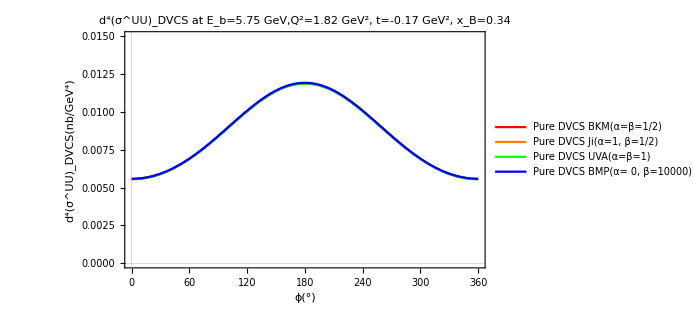

```mathematica
Plot[{
1/2(Γ*2π*389.9*1000* 𝒯DVCSSquared[1/2,0,0]+Γ*2π*389.9*1000* 𝒯DVCSSquared[-1/2,0,0])/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeBKMSetting,
1/2(Γ*2π*389.9*1000* 𝒯DVCSSquared[1/2,0,0]+Γ*2π*389.9*1000* 𝒯DVCSSquared[-1/2,0,0])/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeJiSetting,
1/2(Γ*2π*389.9*1000* 𝒯DVCSSquared[1/2,0,0]+Γ*2π*389.9*1000* 𝒯DVCSSquared[-1/2,0,0])/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeUVASetting,
1/2(Γ*2π*389.9*1000* 𝒯DVCSSquared[1/2,0,0]+Γ*2π*389.9*1000* 𝒯DVCSSquared[-1/2,0,0])/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeBMPSetting
},
{ϕp,0,360},
PlotLegends->Placed[
LineLegend[
{
"Pure DVCS BKM(α=β=1/2)",
"Pure DVCS Ji(α=1, β=1/2)",
"Pure DVCS UVA(α=β=1)",
"Pure DVCS BMP(α= 0, β=10000)"
},
LegendLayout->{"Row",2}
],
{0.5,0.4}],
FrameStyle->Black,
FrameLabel->{"ϕ(°)","d^4(σ^UU)_DVCS(nb/GeV^4)"},
PlotStyle->{Red, Orange, Green, Blue},
PlotLabel->"d^4(σ^UU)_DVCS at E_b=5.75 GeV,Q^2=1.82 GeV^2, t=-0.17 GeV^2, x_B=0.34",
PlotRange->{0.000,0.015},
PlotTheme -> "Scientific"]

Export[
"ji_dvcs_unpolarized_beam_unpolarized_target_kinematic_bin_1.csv",
Table[
Re[
1/2(Γ*2π*389.9*1000* 𝒯DVCSSquared[1/2,0,0]+Γ*2π*389.9*1000* 𝒯DVCSSquared[-1/2,0,0])/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeBKMSetting
],
{ϕp,0,360,1}],
"CSV"];
```

#### (#8.1.1.2): Pure DVCS | Unpolarized Beam | Unpolarized Target | Kinematic Setting 1 @ 10.59 GeV

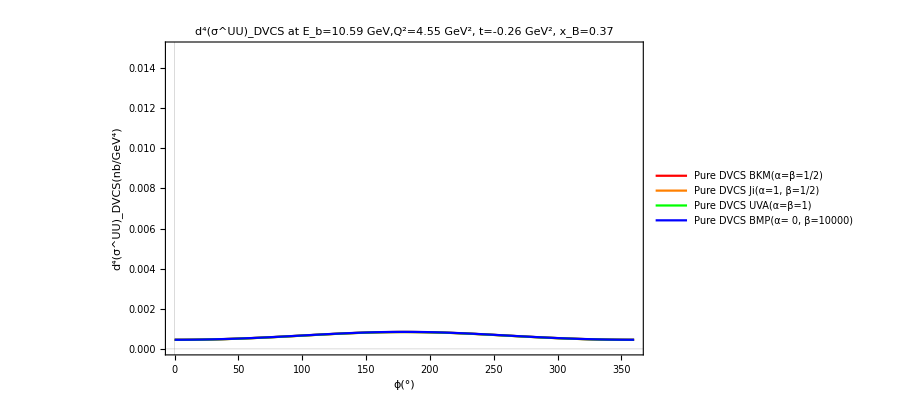

```mathematica
Plot[{
1/2 Γ*2π*389.9*1000*( 𝒯DVCSSquared[1/2,0,0]+ 𝒯DVCSSquared[-1/2,0,0])/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeBKMSetting,
1/2 Γ*2π*389.9*1000*( 𝒯DVCSSquared[1/2,0,0]+ 𝒯DVCSSquared[-1/2,0,0])/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeJiSetting,
1/2 Γ*2π*389.9*1000*( 𝒯DVCSSquared[1/2,0,0]+ 𝒯DVCSSquared[-1/2,0,0])/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeUVASetting,
1/2 Γ*2π*389.9*1000*( 𝒯DVCSSquared[1/2,0,0]+ 𝒯DVCSSquared[-1/2,0,0])/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeBMPSetting
},
{ϕp,0,360},
PlotLegends->Placed[
LineLegend[
{
"Pure DVCS BKM(α=β=1/2)",
"Pure DVCS Ji(α=1, β=1/2)",
"Pure DVCS UVA(α=β=1)",
"Pure DVCS BMP(α= 0, β=10000)"
},
LegendLayout->{"Row",4}
],
{0.5,0.4}],
FrameStyle->Black,
FrameLabel->{"ϕ(°)","d^4(σ^UU)_DVCS(nb/GeV^4)"},
PlotStyle->{Red, Orange, Green, Blue},
PlotLabel->"d^4(σ^UU)_DVCS at E_b=10.59 GeV,Q^2=4.55 GeV^2, t=-0.26 GeV^2, x_B=0.37",
PlotRange->{0.000,0.015},
PlotTheme -> "Scientific"]

Export[
"ji_dvcs_unpolarized_beam_unpolarized_target_kinematic_bin_2.csv",
Table[
Re[
1/2 Γ*2π*389.9*1000*(𝒯DVCSSquared[1/2,0,0]+ 𝒯DVCSSquared[-1/2,0,0])/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeBKMSetting
],
{ϕp,0,360,1}],
"CSV"];
```

### (#8.1.2): Pure DVCS | (+) Polarized Beam | Unpolarized Target:

#### (#8.1.2.1): Pure DVCS | (+) Polarized Beam | Unpolarized Target | Kinematic Setting 1 @ 5.75 GeV

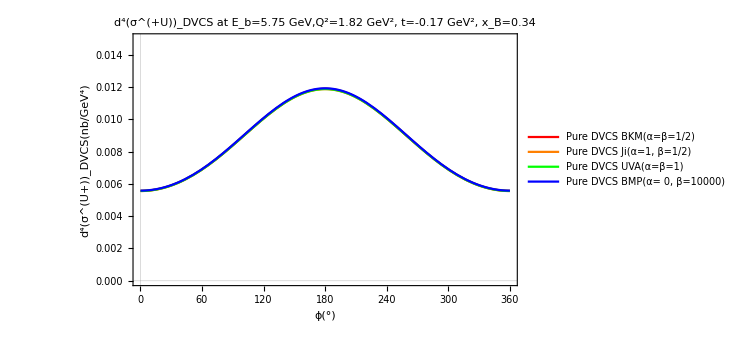

```mathematica
Plot[{
(Γ*2π*389.9*1000* 𝒯DVCSSquared[1/2,0,0])/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeBKMSetting,(Γ*2π*389.9*1000* 𝒯DVCSSquared[1/2,0,0])/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeJiSetting,
(Γ*2π*389.9*1000* 𝒯DVCSSquared[1/2,0,0])/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeUVASetting,
(Γ*2π*389.9*1000* 𝒯DVCSSquared[1/2,0,0])/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeBMPSetting
},
{ϕp,0,360},
PlotLegends->Placed[
LineLegend[
{
"Pure DVCS BKM(α=β=1/2)",
"Pure DVCS Ji(α=1, β=1/2)",
"Pure DVCS UVA(α=β=1)",
"Pure DVCS BMP(α= 0, β=10000)"
},
LegendLayout->{"Row",2}
],
{0.5,0.4}],
FrameStyle->Black,
FrameLabel->{"ϕ(°)","d^4(σ^(U+))_DVCS(nb/GeV^4)"},
PlotStyle->{Red, Orange, Green, Blue},
PlotLabel->"d^4(σ^(+U))_DVCS at E_b=5.75 GeV,Q^2=1.82 GeV^2, t=-0.17 GeV^2, x_B=0.34",
PlotRange->{0.000,0.015},
PlotTheme -> "Scientific"]

Export[
"ji_dvcs_plus_beam_unpolarized_target_kinematic_bin_1.csv",
Table[
Re[
Γ*2π*389.9*1000* 𝒯DVCSSquared[1/2,0,0]/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeBKMSetting
],
{ϕp,0,360,1}],
"CSV"];
```

#### (#8.1.2.2): Pure DVCS | (+) Polarized Beam | Unpolarized Target | Kinematic Setting 1 @ 10.59 GeV

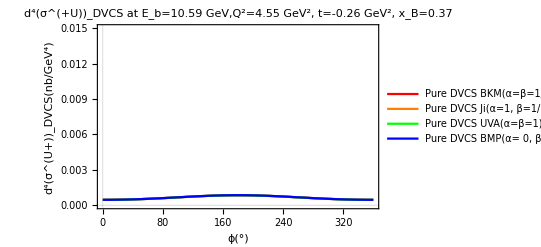

```mathematica
Plot[{
(Γ*2π*389.9*1000* 𝒯DVCSSquared[1/2,0,0])/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeBKMSetting,
(Γ*2π*389.9*1000* 𝒯DVCSSquared[1/2,0,0])/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeJiSetting,
(Γ*2π*389.9*1000* 𝒯DVCSSquared[1/2,0,0])/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeUVASetting,
(Γ*2π*389.9*1000* 𝒯DVCSSquared[1/2,0,0])/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeBMPSetting
},
{ϕp,0,360},
PlotLegends->Placed[
LineLegend[
{
"Pure DVCS BKM(α=β=1/2)",
"Pure DVCS Ji(α=1, β=1/2)",
"Pure DVCS UVA(α=β=1)",
"Pure DVCS BMP(α= 0, β=10000)"
},
LegendLayout->{"Row",2}
],
{0.5,0.4}],
FrameStyle->Black,
FrameLabel->{"ϕ(°)","d^4(σ^(U+))_DVCS(nb/GeV^4)"},
PlotStyle->{Red, Orange, Green, Blue},
PlotLabel->"d^4(σ^(+U))_DVCS at E_b=10.59 GeV,Q^2=4.55 GeV^2, t=-0.26 GeV^2, x_B=0.37",
PlotRange->{0.000,0.015},
PlotTheme -> "Scientific"]

Export[
"ji_dvcs_plus_beam_unpolarized_target_kinematic_bin_2.csv",
Table[
Re[
Γ*2π*389.9*1000* 𝒯DVCSSquared[1/2,0,0]/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeBKMSetting
],
{ϕp,0,360,1}],
"CSV"];
```

### (#8.1.3): Pure DVCS | (-) Polarized Beam | Unpolarized Target:

#### (#8.1.3.1): Pure DVCS | (-) Polarized Beam | Unpolarized Target | Kinematic Setting 1 @ 5.75 GeV

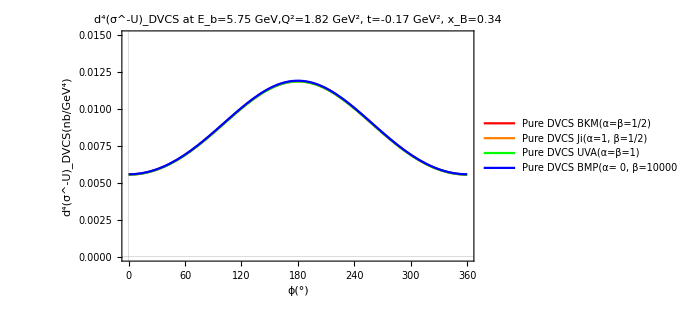

```mathematica
Plot[{
(Γ*2π*389.9*1000* 𝒯DVCSSquared[-1/2,0,0])/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeBKMSetting,
(Γ*2π*389.9*1000* 𝒯DVCSSquared[-1/2,0,0])/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeJiSetting,
(Γ*2π*389.9*1000* 𝒯DVCSSquared[-1/2,0,0])/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeUVASetting,
(Γ*2π*389.9*1000* 𝒯DVCSSquared[-1/2,0,0])/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeBMPSetting
},
{ϕp,0,360},
PlotLegends->Placed[
LineLegend[
{
"Pure DVCS BKM(α=β=1/2)",
"Pure DVCS Ji(α=1, β=1/2)",
"Pure DVCS UVA(α=β=1)",
"Pure DVCS BMP(α= 0, β=10000)"
},
LegendLayout->{"Row",2}
],
{0.5,0.4}],
FrameStyle->Black,
FrameLabel->{"ϕ(°)","d^4(σ^-U)_DVCS(nb/GeV^4)"},
PlotStyle->{Red, Orange, Green, Blue},
PlotLabel->"d^4(σ^-U)_DVCS at E_b=5.75 GeV,Q^2=1.82 GeV^2, t=-0.17 GeV^2, x_B=0.34",
PlotRange->{0.000,0.015},
PlotTheme -> "Scientific"]

Export[
"ji_dvcs_minus_beam_unpolarized_target_kinematic_bin_1.csv",
Table[
Re[
Γ*2π*389.9*1000* 𝒯DVCSSquared[-1/2,0,0]/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeBKMSetting
],
{ϕp,0,360,1}],
"CSV"];
```

#### (#8.1.3.2): Pure DVCS | (-) Polarized Beam | Unpolarized Target | Kinematic Setting 1 @ 10.59 GeV

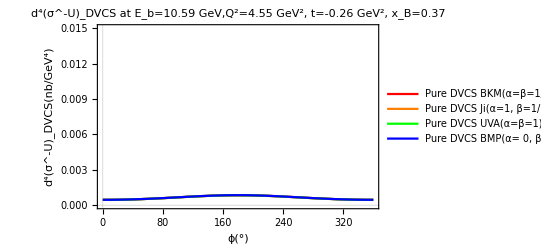

```mathematica
Plot[{
(Γ*2π*389.9*1000* 𝒯DVCSSquared[-1/2,0,0])/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeBKMSetting,
(Γ*2π*389.9*1000* 𝒯DVCSSquared[-1/2,0,0])/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeJiSetting,
(Γ*2π*389.9*1000* 𝒯DVCSSquared[-1/2,0,0])/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeUVASetting,
(Γ*2π*389.9*1000* 𝒯DVCSSquared[-1/2,0,0])/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeBMPSetting
},
{ϕp,0,360},
PlotLegends->Placed[
LineLegend[
{
"Pure DVCS BKM(α=β=1/2)",
"Pure DVCS Ji(α=1, β=1/2)",
"Pure DVCS UVA(α=β=1)",
"Pure DVCS BMP(α= 0, β=10000)"
},
LegendLayout->{"Row",2}
],
{0.5,0.4}],
FrameStyle->Black,
FrameLabel->{"ϕ(°)","d^4(σ^-U)_DVCS(nb/GeV^4)"},
PlotStyle->{Red, Orange, Green, Blue},
PlotLabel->"d^4(σ^-U)_DVCS at E_b=10.59 GeV,Q^2=4.55 GeV^2, t=-0.26 GeV^2, x_B=0.37",
PlotRange->{0.000,0.015},
PlotTheme -> "Scientific"]

Export[
"ji_dvcs_minus_beam_unpolarized_target_kinematic_bin_2.csv",
Table[
Re[
Γ*2π*389.9*1000* 𝒯DVCSSquared[-1/2,0,0]/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeBKMSetting
],
{ϕp,0,360,1}],
"CSV"];
```

### (#8.1.4): Pure DVCS | Unpolarized Beam | Longitudinally-Polarized Target:

#### (#8.1.4.1): Pure DVCS | Unpolarized Beam | Longitudinally-Polarized Target | Kinematic Setting 1 @ 5.75 GeV

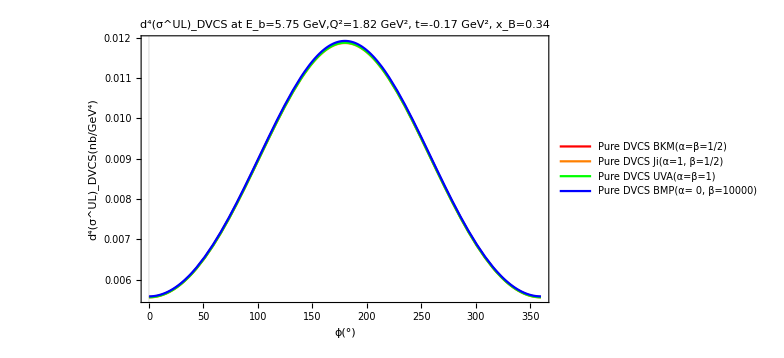

```mathematica
Plot[{
Γ*2π*389.9*1000*1/2(𝒯DVCSSquared[1/2,1,0]+ 𝒯DVCSSquared[-1/2,1,0])/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeBKMSetting,
Γ*2π*389.9*1000*1/2(𝒯DVCSSquared[1/2,1,0]+ 𝒯DVCSSquared[-1/2,1,0])/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeJiSetting,
Γ*2π*389.9*1000*1/2(𝒯DVCSSquared[1/2,1,0]+ 𝒯DVCSSquared[-1/2,1,0])/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeUVASetting,
Γ*2π*389.9*1000*1/2(𝒯DVCSSquared[1/2,1,0]+ 𝒯DVCSSquared[-1/2,1,0])/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeBMPSetting
},
{ϕp,0,360},
PlotLegends->Placed[
LineLegend[
{
"Pure DVCS BKM(α=β=1/2)",
"Pure DVCS Ji(α=1, β=1/2)",
"Pure DVCS UVA(α=β=1)",
"Pure DVCS BMP(α= 0, β=10000)"
},
LegendLayout->{"Row",4}
],
{0.2,0.8}],
FrameStyle->Black,
FrameLabel->{"ϕ(°)","d^4(σ^UL)_DVCS(nb/GeV^4)"},
PlotStyle->{Red, Orange, Green, Blue},
PlotLabel->"d^4(σ^UL)_DVCS at E_b=5.75 GeV,Q^2=1.82 GeV^2, t=-0.17 GeV^2, x_B=0.34",
PlotRange->Full,
PlotTheme -> "Scientific"]

Export[
"ji_dvcs_unpolarized_beam_lp_target_kinematic_bin_1.csv",
Table[
Re[Γ*2π*389.9*1000*1/2(𝒯DVCSSquared[1/2,1,0]+ 𝒯DVCSSquared[-1/2,1,0])/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeBKMSetting
],
{ϕp,0,360,1}],
"CSV"];
```

#### (#8.1.4.2): Pure DVCS | Unpolarized Beam | Longitudinally-Polarized Target | Kinematic Setting 1 @ 10.59 GeV

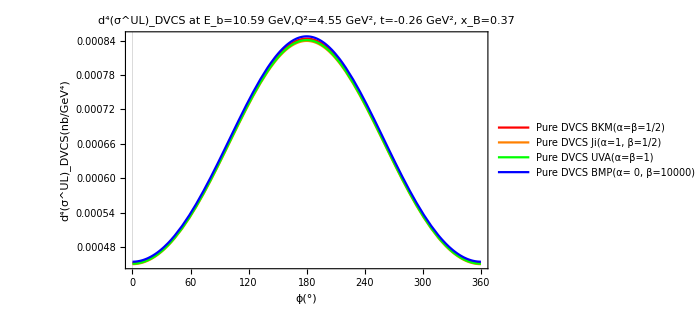

```mathematica
Plot[{
1/2(Γ*2π*389.9*1000* 𝒯DVCSSquared[1/2,1,0]+Γ*2π*389.9*1000* 𝒯DVCSSquared[-1/2,1,0])/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeBKMSetting,
1/2(Γ*2π*389.9*1000* 𝒯DVCSSquared[1/2,1,0]+Γ*2π*389.9*1000* 𝒯DVCSSquared[-1/2,1,0])/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeJiSetting,
1/2(Γ*2π*389.9*1000* 𝒯DVCSSquared[1/2,1,0]+Γ*2π*389.9*1000* 𝒯DVCSSquared[-1/2,1,0])/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeUVASetting,
1/2(Γ*2π*389.9*1000* 𝒯DVCSSquared[1/2,1,0]+Γ*2π*389.9*1000* 𝒯DVCSSquared[-1/2,1,0])/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeBMPSetting
},
{ϕp,0,360},
PlotLegends->Placed[
LineLegend[
{
"Pure DVCS BKM(α=β=1/2)",
"Pure DVCS Ji(α=1, β=1/2)",
"Pure DVCS UVA(α=β=1)",
"Pure DVCS BMP(α= 0, β=10000)"
},
LegendLayout->{"Row",4}
],
{0.2,0.8}],
FrameStyle->Black,
FrameLabel->{"ϕ(°)","d^4(σ^UL)_DVCS(nb/GeV^4)"},
PlotStyle->{Red, Orange, Green, Blue},
PlotLabel->"d^4(σ^UL)_DVCS at E_b=10.59 GeV,Q^2=4.55 GeV^2, t=-0.26 GeV^2, x_B=0.37",
PlotRange->Full,
PlotTheme -> "Scientific"]

Export[
"ji_dvcs_unpolarized_beam_lp_target_kinematic_bin_2.csv",
Table[
Re[1/2(Γ*2π*389.9*1000* 𝒯DVCSSquared[1/2,1,0]+Γ*2π*389.9*1000* 𝒯DVCSSquared[-1/2,1,0])/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeBKMSetting
],
{ϕp,0,360,1}],
"CSV"];
```

### (#8.1.5): Pure DVCS | (+) Polarized Beam | Longitudinally-Polarized Target:

#### (#8.1.5.1): Pure DVCS | (+) Polarized Beam | Longitudinally-Polarized Target | Kinematic Setting 1 @ 5.75 GeV

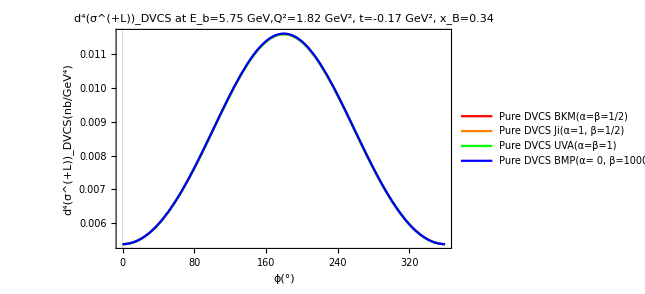

```mathematica
Plot[{
(Γ*2π*389.9*1000* 𝒯DVCSSquared[1/2,1,0])/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeBKMSetting,
(Γ*2π*389.9*1000* 𝒯DVCSSquared[1/2,1,0])/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeJiSetting,
(Γ*2π*389.9*1000* 𝒯DVCSSquared[1/2,1,0])/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeUVASetting,
(Γ*2π*389.9*1000* 𝒯DVCSSquared[1/2,1,0])/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeBMPSetting
},
{ϕp,0,360},
PlotLegends->Placed[
LineLegend[
{
"Pure DVCS BKM(α=β=1/2)",
"Pure DVCS Ji(α=1, β=1/2)",
"Pure DVCS UVA(α=β=1)",
"Pure DVCS BMP(α= 0, β=10000)"
},
LegendLayout->{"Row",4}
],
{0.2,0.8}],
FrameStyle->Black,
FrameLabel->{"ϕ(°)","d^4(σ^(+L))_DVCS(nb/GeV^4)"},
PlotStyle->{Red, Orange, Green, Blue},
PlotLabel->"d^4(σ^(+L))_DVCS at E_b=5.75 GeV,Q^2=1.82 GeV^2, t=-0.17 GeV^2, x_B=0.34",
PlotRange->Full,
PlotTheme -> "Scientific"]

Export[
"ji_dvcs_plus_beam_lp_target_kinematic_bin_1.csv",
Table[
Re[
(Γ*2π*389.9*1000* 𝒯DVCSSquared[1/2,1,0])/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeBKMSetting
],
{ϕp,0,360,1}],
"CSV"];
```

#### (#8.1.5.2): Pure DVCS | (+) Polarized Beam | Longitudinally-Polarized Target | Kinematic Setting 1 @ 10.59 GeV

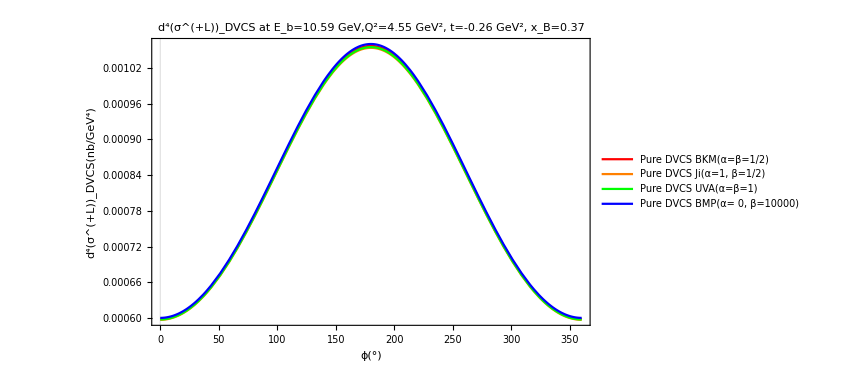

```mathematica
Plot[{
(Γ*2π*389.9*1000* 𝒯DVCSSquared[1/2,1,0])/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeBKMSetting,
(Γ*2π*389.9*1000* 𝒯DVCSSquared[1/2,1,0])/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeJiSetting,
(Γ*2π*389.9*1000* 𝒯DVCSSquared[1/2,1,0])/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeUVASetting,
(Γ*2π*389.9*1000* 𝒯DVCSSquared[1/2,1,0])/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeBMPSetting
},
{ϕp,0,360},
PlotLegends->Placed[
LineLegend[
{
"Pure DVCS BKM(α=β=1/2)",
"Pure DVCS Ji(α=1, β=1/2)",
"Pure DVCS UVA(α=β=1)",
"Pure DVCS BMP(α= 0, β=10000)"
},
LegendLayout->{"Row",4}
],
{0.2,0.8}],
FrameStyle->Black,
FrameLabel->{"ϕ(°)","d^4(σ^(+L))_DVCS(nb/GeV^4)"},
PlotStyle->{Red, Orange, Green, Blue},
PlotLabel->"d^4(σ^(+L))_DVCS at E_b=10.59 GeV,Q^2=4.55 GeV^2, t=-0.26 GeV^2, x_B=0.37",
PlotRange->Full,
PlotTheme -> "Scientific"]

Export[
"ji_dvcs_plus_beam_lp_target_kinematic_bin_2.csv",
Table[
Re[
(Γ*2π*389.9*1000* 𝒯DVCSSquared[1/2,1,0])/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeBKMSetting
],
{ϕp,0,360,1}],
"CSV"];
```

### (#8.1.6): Pure DVCS | (-) Polarized Beam | Longitudinally-Polarized Target:

#### (#8.1.6.1): Pure DVCS | (-) Polarized Beam | Longitudinally-Polarized Target | Kinematic Setting 1 @ 5.75 GeV

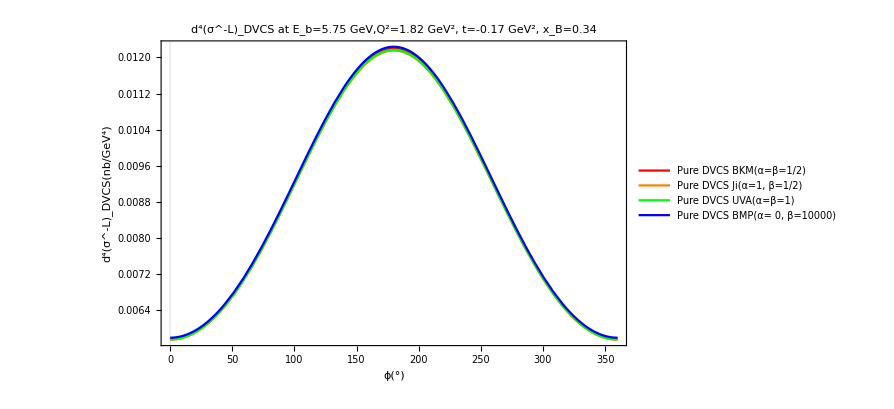

```mathematica
Plot[{
(Γ*2π*389.9*1000* 𝒯DVCSSquared[-1/2,1,0])/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeBKMSetting,
(Γ*2π*389.9*1000* 𝒯DVCSSquared[-1/2,1,0])/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeJiSetting,
(Γ*2π*389.9*1000* 𝒯DVCSSquared[-1/2,1,0])/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeUVASetting,
(Γ*2π*389.9*1000* 𝒯DVCSSquared[-1/2,1,0])/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeBMPSetting
},
{ϕp,0,360},
PlotLegends->Placed[
LineLegend[
{
"Pure DVCS BKM(α=β=1/2)",
"Pure DVCS Ji(α=1, β=1/2)",
"Pure DVCS UVA(α=β=1)",
"Pure DVCS BMP(α= 0, β=10000)"
},
LegendLayout->{"Row",4}
],
{0.2,0.8}],
FrameStyle->Black,
FrameLabel->{"ϕ(°)","d^4(σ^-L)_DVCS(nb/GeV^4)"},
PlotStyle->{Red, Orange, Green, Blue},
PlotLabel->"d^4(σ^-L)_DVCS at E_b=5.75 GeV,Q^2=1.82 GeV^2, t=-0.17 GeV^2, x_B=0.34",
PlotRange->Full,
PlotTheme -> "Scientific"]

Export[
"ji_dvcs_minus_beam_lp_target_kinematic_bin_1_v3.csv",
Table[
Re[
(Γ*2π*389.9*1000* 𝒯DVCSSquared[-1/2,1,0])/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeBKMSetting
],
{ϕp,0,360,1}],
"CSV"];
```

#### (#8.1.6.1): Pure DVCS | (-) Polarized Beam | Longitudinally-Polarized Target | Kinematic Setting 1 @ 10.59 GeV

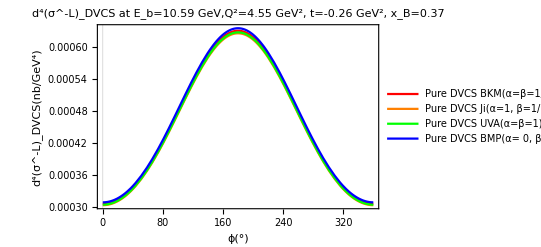

```mathematica
Plot[{
(Γ*2π*389.9*1000* 𝒯DVCSSquared[-1/2,1,0])/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeBKMSetting,
(Γ*2π*389.9*1000* 𝒯DVCSSquared[-1/2,1,0])/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeJiSetting,
(Γ*2π*389.9*1000* 𝒯DVCSSquared[-1/2,1,0])/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeUVASetting,
(Γ*2π*389.9*1000* 𝒯DVCSSquared[-1/2,1,0])/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeBMPSetting
},
{ϕp,0,360},
PlotLegends->Placed[
LineLegend[
{
"Pure DVCS BKM(α=β=1/2)",
"Pure DVCS Ji(α=1, β=1/2)",
"Pure DVCS UVA(α=β=1)",
"Pure DVCS BMP(α= 0, β=10000)"
},
LegendLayout->{"Row",4}
],
{0.2,0.8}],
FrameStyle->Black,
FrameLabel->{"ϕ(°)","d^4(σ^-L)_DVCS(nb/GeV^4)"},
PlotStyle->{Red, Orange, Green, Blue},
PlotLabel->"d^4(σ^-L)_DVCS at E_b=10.59 GeV,Q^2=4.55 GeV^2, t=-0.26 GeV^2, x_B=0.37",
PlotRange->Full,
PlotTheme -> "Scientific"]

Export[
"ji_dvcs_minus_beam_lp_target_kinematic_bin_2.csv",
Table[
Re[
(Γ*2π*389.9*1000* 𝒯DVCSSquared[-1/2,1,0])/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeBKMSetting
],
{ϕp,0,360,1}],
"CSV"];
```

## (#8.2): Pure Interference:

### (#8.2.1): Pure Interference | Unpolarized Beam | Unpolarized Target:

#### (#8.2.1.1): Pure Interference | Unpolarized Beam | Unpolarized Target | Kinematic Setting 1 @ 5.75 GeV

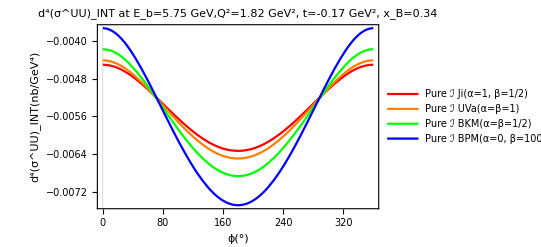

```mathematica
Plot[{
Γ*2π*389.9*1000* 1/2(ℐ[1/2,0,0]+ℐ[-1/2,0,0])/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeJiSetting,
Γ*2π*389.9*1000* 1/2(ℐ[1/2,0,0]+ℐ[-1/2,0,0])/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeUVASetting,
Γ*2π*389.9*1000* 1/2(ℐ[1/2,0,0]+ℐ[-1/2,0,0])/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeBKMSetting,
Γ*2π*389.9*1000* 1/2(ℐ[1/2,0,0]+ℐ[-1/2,0,0])/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeBMPSetting},
{ϕp,0,360},
PlotLegends->Placed[
LineLegend[
{"Pure ℐ Ji(α=1, β=1/2)",
"Pure ℐ UVa(α=β=1)",
"Pure ℐ BKM(α=β=1/2)",
"Pure ℐ BPM(α=0, β=10000)"},
LegendLayout->{"Row",4}
],
{0.78,0.78}],
ImageSize->Automatic,
FrameStyle->Black,
FrameLabel->{"ϕ(°)","d^4(σ^UU)_INT(nb/GeV^4)"},
PlotStyle->{Red, Orange,Green, Blue},
PlotLabel->"d^4(σ^UU)_INT at E_b=5.75 GeV,Q^2=1.82 GeV^2, t=-0.17 GeV^2, x_B=0.34",
PlotRange->{0.0, -0.008},
PlotTheme -> "Scientific"]

Export[
"ji_interference_unpolarized_beam_unpolarized_target_kinematic_bin_1.csv",
Table[
Re[
Γ*2π*389.9*1000*  1/2(ℐ[1/2,0,0]+ℐ[-1/2,0,0])/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeBKMSetting
],
{ϕp,0,360,1}],
"CSV"];
```

#### (#8.2.1.1): Pure Interference | Unpolarized Beam | Unpolarized Target | Kinematic Setting 1 @ 10.59 GeV

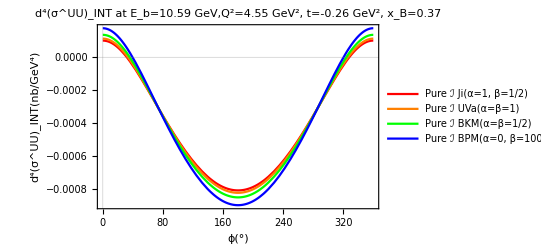

```mathematica
Plot[{
Γ*2π*389.9*1000* 1/2(ℐ[1/2,0,0]+ℐ[-1/2,0,0])/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeJiSetting,
Γ*2π*389.9*1000*  1/2(ℐ[1/2,0,0]+ℐ[-1/2,0,0])/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeUVASetting,
Γ*2π*389.9*1000*  1/2(ℐ[1/2,0,0]+ℐ[-1/2,0,0])/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeBKMSetting,
Γ*2π*389.9*1000* 1/2(ℐ[1/2,0,0]+ℐ[-1/2,0,0])/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeBMPSetting},
{ϕp,0,360},
PlotLegends->{
"Pure ℐ Ji(α=1, β=1/2)",
"Pure ℐ UVa(α=β=1)",
"Pure ℐ BKM(α=β=1/2)",
"Pure ℐ BPM(α=0, β=10000)"
},
ImageSize->Automatic,
FrameStyle->Black,
FrameLabel->{"ϕ(°)","d^4(σ^UU)_INT(nb/GeV^4)"},
PlotStyle->{Red, Orange,Green, Blue},
PlotLabel->"d^4(σ^UU)_INT at E_b=10.59 GeV,Q^2=4.55 GeV^2, t=-0.26 GeV^2, x_B=0.37",
PlotTheme -> "Scientific"]

Export[
"ji_interference_unpolarized_beam_unpolarized_target_kinematic_bin_2.csv",
Table[
Re[
Γ*2π*389.9*1000*  1/2(ℐ[1/2,0,0]+ℐ[-1/2,0,0])/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeBKMSetting
],
{ϕp,0,360,1}],
"CSV"];
```

### (#X.2.1): Pure Interference | (+) Polarized Beam | Unpolarized Target:

#### (#8.2.1.1): Pure Interference | (+) Polarized Beam | Unpolarized Target | Kinematic Setting 1 @ 5.75 GeV

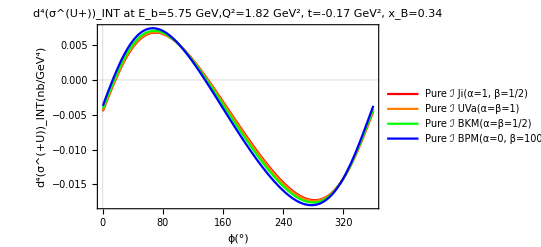

```mathematica
Plot[{
Γ*2π*389.9*1000* ℐ[1/2,0,0]/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeJiSetting,
Γ*2π*389.9*1000* ℐ[1/2,0,0]/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeUVASetting,
Γ*2π*389.9*1000* ℐ[1/2,0,0]/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeBKMSetting,
Γ*2π*389.9*1000* ℐ[1/2,0,0]/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeBMPSetting},
{ϕp,0,360},
PlotLegends->{
"Pure ℐ Ji(α=1, β=1/2)",
"Pure ℐ UVa(α=β=1)",
"Pure ℐ BKM(α=β=1/2)",
"Pure ℐ BPM(α=0, β=10000)"
},
FrameStyle->Black,
FrameLabel->{"ϕ(°)","d^4(σ^(+U))_INT(nb/GeV^4)"},
PlotStyle->{Red, Orange,Green, Blue},
PlotLabel->"d^4(σ^(U+))_INT at E_b=5.75 GeV,Q^2=1.82 GeV^2, t=-0.17 GeV^2, x_B=0.34",
PlotRange->Full,
PlotTheme -> "Scientific"]

Export[
"ji_interference_plus_beam_unpolarized_target_kinematic_bin_1.csv",
Table[
Re[
Γ*2π*389.9*1000* ℐ[1/2,0,0]/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeBKMSetting
],
{ϕp,0,360,1}],
"CSV"];
```

#### (#8.2.1.1): Pure Interference | (+) Polarized Beam | Unpolarized Target | Kinematic Setting 1 @ 10.59 GeV

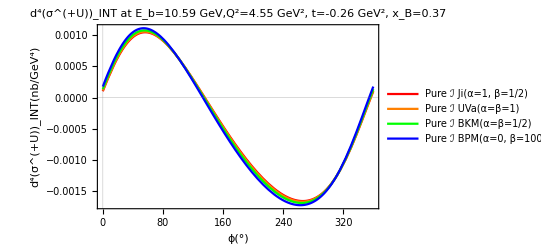

```mathematica
Plot[{
Γ*2π*389.9*1000* ℐ[1/2,0,0]/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeJiSetting,
Γ*2π*389.9*1000* ℐ[1/2,0,0]/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeUVASetting,
Γ*2π*389.9*1000* ℐ[1/2,0,0]/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeBKMSetting,
Γ*2π*389.9*1000* ℐ[1/2,0,0]/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeBMPSetting},
{ϕp,0,360},
PlotLegends->{
"Pure ℐ Ji(α=1, β=1/2)",
"Pure ℐ UVa(α=β=1)",
"Pure ℐ BKM(α=β=1/2)",
"Pure ℐ BPM(α=0, β=10000)"
},
FrameStyle->Black,
FrameLabel->{"ϕ(°)","d^4(σ^(+U))_INT(nb/GeV^4)"},
PlotStyle->{Red, Orange,Green, Blue},
PlotLabel->"d^4(σ^(+U))_INT at E_b=10.59 GeV,Q^2=4.55 GeV^2, t=-0.26 GeV^2, x_B=0.37",
PlotRange->Full,
PlotTheme -> "Scientific"]

Export[
"ji_interference_plus_beam_unpolarized_target_kinematic_bin_2.csv",
Table[
Re[
Γ*2π*389.9*1000* ℐ[1/2,0,0]/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeBKMSetting
],
{ϕp,0,360,1}],
"CSV"];
```

### (#X.2.1): Pure Interference | (-) Polarized Beam | Unpolarized Target:

#### (#8.2.1.1): Pure Interference | (-) Polarized Beam | Unpolarized Target | Kinematic Setting 1 @ 5.75 GeV

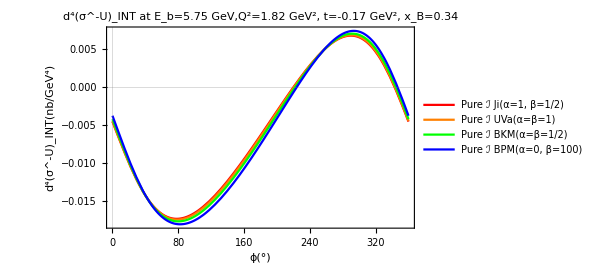

```mathematica
Plot[{
Γ*2π*389.9*1000* ℐ[-1/2,0,0]/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeJiSetting,
Γ*2π*389.9*1000* ℐ[-1/2,0,0]/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeUVASetting,
Γ*2π*389.9*1000* ℐ[-1/2,0,0]/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeBKMSetting,
Γ*2π*389.9*1000* ℐ[-1/2,0,0]/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeBMPSetting},
{ϕp,0,360},
PlotLegends->Placed[
LineLegend[
{"Pure ℐ Ji(α=1, β=1/2)",
"Pure ℐ UVa(α=β=1)",
"Pure ℐ BKM(α=β=1/2)",
"Pure ℐ BPM(α=0, β=100)"},
LegendLayout->{"Row",4}
],
{0.28,0.78}],
FrameStyle->Black,
FrameLabel->{"ϕ(°)","d^4(σ^-U)_INT(nb/GeV^4)"},
PlotStyle->{Red, Orange,Green, Blue},
PlotLabel->"d^4(σ^-U)_INT at E_b=5.75 GeV,Q^2=1.82 GeV^2, t=-0.17 GeV^2, x_B=0.34",
PlotRange->Full,
PlotTheme -> "Scientific"]

Export[
"ji_interference_minus_beam_unpolarized_target_kinematic_bin_1.csv",
Table[
Re[
Γ*2π*389.9*1000* ℐ[-1/2,0,0]/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeBKMSetting
],
{ϕp,0,360,1}],
"CSV"];
```

#### (#8.2.1.1): Pure Interference | (-) Polarized Beam | Unpolarized Target | Kinematic Setting 1 @ 10.59 GeV

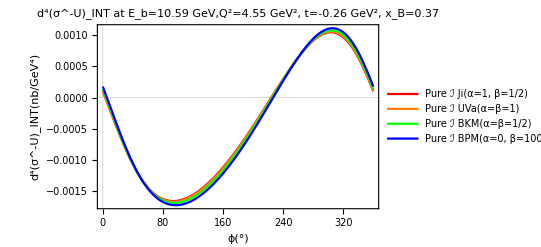

```mathematica
Plot[{
Γ*2π*389.9*1000* ℐ[-1/2,0,0]/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeJiSetting,
Γ*2π*389.9*1000* ℐ[-1/2,0,0]/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeUVASetting,
Γ*2π*389.9*1000* ℐ[-1/2,0,0]/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeBKMSetting,
Γ*2π*389.9*1000* ℐ[-1/2,0,0]/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeBMPSetting},
{ϕp,0,360},
PlotLegends->Placed[
LineLegend[
{"Pure ℐ Ji(α=1, β=1/2)",
"Pure ℐ UVa(α=β=1)",
"Pure ℐ BKM(α=β=1/2)",
"Pure ℐ BPM(α=0, β=100)"},
LegendLayout->{"Row",4}
],
{0.28,0.78}],
FrameStyle->Black,
FrameLabel->{"ϕ(°)","d^4(σ^-U)_INT(nb/GeV^4)"},
PlotStyle->{Red, Orange,Green, Blue},
PlotLabel->"d^4(σ^-U)_INT at E_b=10.59 GeV,Q^2=4.55 GeV^2, t=-0.26 GeV^2, x_B=0.37",
PlotRange->Full,
PlotTheme -> "Scientific"]

Export[
"ji_interference_minus_beam_unpolarized_target_kinematic_bin_2.csv",
Table[
Re[
Γ*2π*389.9*1000* ℐ[-1/2,0,0]/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeBKMSetting
],
{ϕp,0,360,1}],
"CSV"];
```

### (#X.2.1): Pure Interference | Unpolarized Beam | Longitudinally-Polarized Target:

#### (#8.2.1.1): Pure Interference | Unpolarized Beam | Longitudinally-Polarized Target | Kinematic Setting 1 @ 5.75 GeV

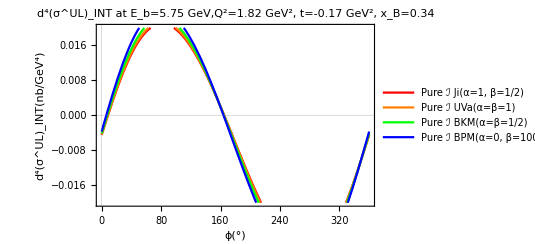

```mathematica
Plot[{
Γ*2π*389.9*1000* 1/2(ℐ[1/2,1,0]+ℐ[-1/2,1,0])/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeJiSetting,
Γ*2π*389.9*1000* 1/2(ℐ[1/2,1,0]+ℐ[-1/2,1,0])/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeUVASetting,
Γ*2π*389.9*1000* 1/2(ℐ[1/2,1,0]+ℐ[-1/2,1,0])/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeBKMSetting,
Γ*2π*389.9*1000* 1/2(ℐ[1/2,1,0]+ℐ[-1/2,1,0])/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeBMPSetting},
{ϕp,0,360},
PlotLegends->Placed[
LineLegend[
{"Pure ℐ Ji(α=1, β=1/2)",
"Pure ℐ UVa(α=β=1)",
"Pure ℐ BKM(α=β=1/2)",
"Pure ℐ BPM(α=0, β=100)"},
LegendLayout->{"Row",4}
],
{0.78,0.78}],
ImageSize->Automatic,
FrameStyle->Black,
FrameLabel->{"ϕ(°)","d^4(σ^UL)_INT(nb/GeV^4)"},
PlotStyle->{Red, Orange,Green, Blue},
PlotLabel->"d^4(σ^UL)_INT at E_b=5.75 GeV,Q^2=1.82 GeV^2, t=-0.17 GeV^2, x_B=0.34",
PlotRange->{0.02, -0.02},
PlotTheme -> "Scientific"]

Export[
"ji_interference_unpolarized_beam_lp_target_kinematic_bin_1_v3.csv",
Table[
Re[
Γ*2π*389.9*1000* 1/2(ℐ[1/2,1,0]+ℐ[-1/2,1,0])/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeBKMSetting
],
{ϕp,0,360,1}],
"CSV"];
```

#### (#8.2.1.1): Pure Interference | Unpolarized Beam | Longitudinally-Polarized Target | Kinematic Setting 1 @ 10.59 GeV

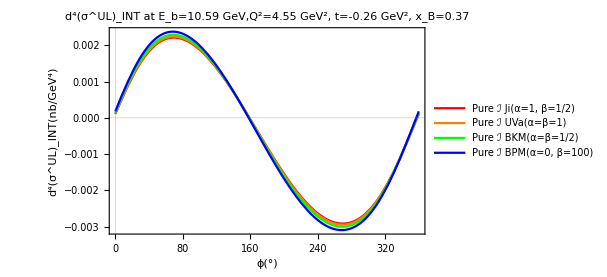

```mathematica
Plot[{
Γ*2π*389.9*1000* 1/2(ℐ[1/2,1,0]+ℐ[-1/2,1,0])/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeJiSetting,
Γ*2π*389.9*1000* 1/2(ℐ[1/2,1,0]+ℐ[-1/2,1,0])/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeUVASetting,
Γ*2π*389.9*1000* 1/2(ℐ[1/2,1,0]+ℐ[-1/2,1,0])/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeBKMSetting,
Γ*2π*389.9*1000* 1/2(ℐ[1/2,1,0]+ℐ[-1/2,1,0])/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeBMPSetting},
{ϕp,0,360},
PlotLegends->Placed[
LineLegend[
{"Pure ℐ Ji(α=1, β=1/2)",
"Pure ℐ UVa(α=β=1)",
"Pure ℐ BKM(α=β=1/2)",
"Pure ℐ BPM(α=0, β=100)"},
LegendLayout->{"Row",4}
],
{0.78,0.78}],
ImageSize->Automatic,
FrameStyle->Black,
FrameLabel->{"ϕ(°)","d^4(σ^UL)_INT(nb/GeV^4)"},
PlotStyle->{Red, Orange,Green, Blue},
PlotLabel->"d^4(σ^UL)_INT at E_b=10.59 GeV,Q^2=4.55 GeV^2, t=-0.26 GeV^2, x_B=0.37",
PlotRange->{0.02, -0.02},
PlotTheme -> "Scientific"]

Export[
"ji_interference_unpolarized_beam_lp_target_kinematic_bin_2_v3.csv",
Table[
Re[
Γ*2π*389.9*1000* 1/2(ℐ[1/2,1,0]+ℐ[-1/2,1,0])/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeBKMSetting
],
{ϕp,0,360,1}],
"CSV"];
```

### (#X.2.1): Pure Interference | (+) Polarized Beam | Longitudinally-Polarized Target:

#### (#8.2.1.1): Pure Interference | (+) Polarized Beam | Longitudinally-Polarized Target | Kinematic Setting 1 @ 5.75 GeV

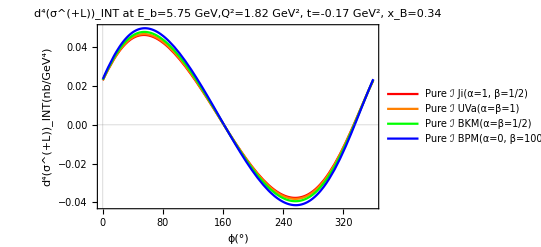

```mathematica
Plot[{
Γ*2π*389.9*1000* ℐ[1/2,1,0]/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeJiSetting,
Γ*2π*389.9*1000* ℐ[1/2,1,0]/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeUVASetting,
Γ*2π*389.9*1000* ℐ[1/2,1,0]/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeBKMSetting,
Γ*2π*389.9*1000* ℐ[1/2,1,0]/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeBMPSetting},
{ϕp,0,360},
PlotLegends->Placed[
LineLegend[
{"Pure ℐ Ji(α=1, β=1/2)",
"Pure ℐ UVa(α=β=1)",
"Pure ℐ BKM(α=β=1/2)",
"Pure ℐ BPM(α=0, β=100)"},
LegendLayout->{"Row",4}
],
{0.78,0.78}],
ImageSize->Automatic,
FrameStyle->Black,
FrameLabel->{"ϕ(°)","d^4(σ^(+L))_INT(nb/GeV^4)"},
PlotStyle->{Red, Orange,Green, Blue},
PlotLabel->"d^4(σ^(+L))_INT at E_b=5.75 GeV,Q^2=1.82 GeV^2, t=-0.17 GeV^2, x_B=0.34",
PlotRange->Automatic,
PlotTheme -> "Scientific"]

Export[
"ji_interference_plus_beam_lp_target_kinematic_bin_1_v3.csv",
Table[
Re[
Γ*2π*389.9*1000* ℐ[1/2,1,0]/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeBKMSetting
],
{ϕp,0,360,1}],
"CSV"];
```

#### (#8.2.1.1): Pure Interference | (+) Polarized Beam | Longitudinally-Polarized Target | Kinematic Setting 1 @ 10.59 GeV

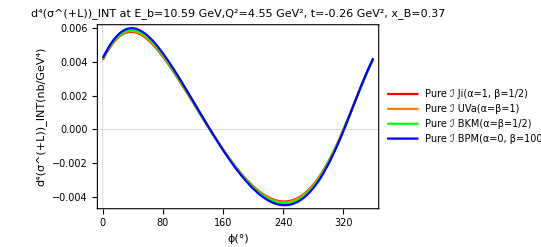

```mathematica
Plot[{
Γ*2π*389.9*1000* ℐ[1/2,1,0]/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeJiSetting,
Γ*2π*389.9*1000* ℐ[1/2,1,0]/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeUVASetting,
Γ*2π*389.9*1000* ℐ[1/2,1,0]/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeBKMSetting,
Γ*2π*389.9*1000* ℐ[1/2,1,0]/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeBMPSetting},
{ϕp,0,360},
PlotLegends->Placed[
LineLegend[
{"Pure ℐ Ji(α=1, β=1/2)",
"Pure ℐ UVa(α=β=1)",
"Pure ℐ BKM(α=β=1/2)",
"Pure ℐ BPM(α=0, β=100)"},
LegendLayout->{"Row",4}
],
{0.78,0.78}],
ImageSize->Automatic,
FrameStyle->Black,
FrameLabel->{"ϕ(°)","d^4(σ^(+L))_INT(nb/GeV^4)"},
PlotStyle->{Red, Orange,Green, Blue},
PlotLabel->"d^4(σ^(+L))_INT at E_b=10.59 GeV,Q^2=4.55 GeV^2, t=-0.26 GeV^2, x_B=0.37",
PlotRange->Automatic,
PlotTheme -> "Scientific"]

Export[
"ji_interference_plus_beam_lp_target_kinematic_bin_2_v3.csv",
Table[
Re[
Γ*2π*389.9*1000* ℐ[1/2,1,0]/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeBKMSetting
],
{ϕp,0,360,1}],
"CSV"];
```

### (#X.2.1): Pure Interference | (-) Polarized Beam | Longitudinally-Polarized Target:

#### (#8.2.1.1): Pure Interference | (-) Polarized Beam | Longitudinally-Polarized Target | Kinematic Setting 1 @ 5.75 GeV

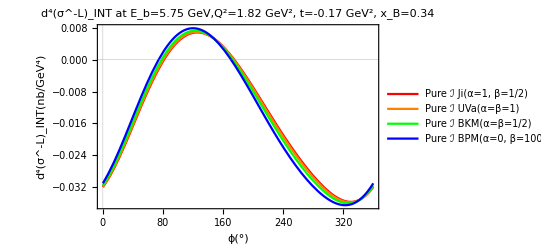

```mathematica
Plot[{
Γ*2π*389.9*1000* ℐ[-1/2,1,0]/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeJiSetting,
Γ*2π*389.9*1000* ℐ[-1/2,1,0]/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeUVASetting,
Γ*2π*389.9*1000* ℐ[-1/2,1,0]/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeBKMSetting,
Γ*2π*389.9*1000* ℐ[-1/2,1,0]/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeBMPSetting},
{ϕp,0,360},
PlotLegends->Placed[
LineLegend[
{"Pure ℐ Ji(α=1, β=1/2)",
"Pure ℐ UVa(α=β=1)",
"Pure ℐ BKM(α=β=1/2)",
"Pure ℐ BPM(α=0, β=100)"},
LegendLayout->{"Row",4}
],
{0.78,0.78}],
ImageSize->Automatic,
FrameStyle->Black,
FrameLabel->{"ϕ(°)","d^4(σ^-L)_INT(nb/GeV^4)"},
PlotStyle->{Red, Orange,Green, Blue},
PlotLabel->"d^4(σ^-L)_INT at E_b=5.75 GeV,Q^2=1.82 GeV^2, t=-0.17 GeV^2, x_B=0.34",
PlotRange->All,
PlotTheme -> "Scientific"]

Export[
"ji_interference_minus_beam_lp_target_kinematic_bin_1_v3.csv",
Table[
Re[
Γ*2π*389.9*1000* ℐ[-1/2,1,0]/.ϕ->ϕp/180*π/.kinematicSetting1/.lightconeBKMSetting
],
{ϕp,0,360, 1}],
"CSV"];
```

#### (#8.2.1.1): Pure Interference | (-) Polarized Beam | Longitudinally-Polarized Target | Kinematic Setting 1 @ 5.75 GeV

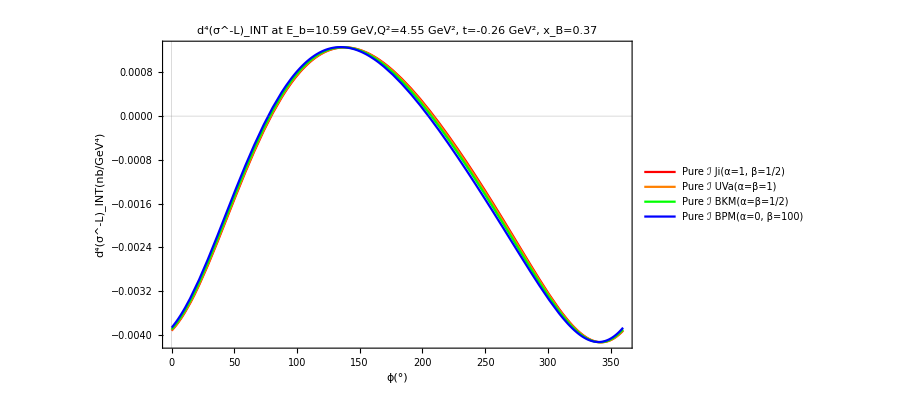

```mathematica
Plot[{
Γ*2π*389.9*1000* ℐ[-1/2,1,0]/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeJiSetting,
Γ*2π*389.9*1000* ℐ[-1/2,1,0]/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeUVASetting,
Γ*2π*389.9*1000* ℐ[-1/2,1,0]/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeBKMSetting,
Γ*2π*389.9*1000* ℐ[-1/2,1,0]/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeBMPSetting},
{ϕp,0,360},
PlotLegends->Placed[
LineLegend[
{"Pure ℐ Ji(α=1, β=1/2)",
"Pure ℐ UVa(α=β=1)",
"Pure ℐ BKM(α=β=1/2)",
"Pure ℐ BPM(α=0, β=100)"},
LegendLayout->{"Row",4}
],
{0.78,0.78}],
ImageSize->Automatic,
FrameStyle->Black,
FrameLabel->{"ϕ(°)","d^4(σ^-L)_INT(nb/GeV^4)"},
PlotStyle->{Red, Orange,Green, Blue},
PlotLabel->"d^4(σ^-L)_INT at E_b=10.59 GeV,Q^2=4.55 GeV^2, t=-0.26 GeV^2, x_B=0.37",
PlotRange->All,
PlotTheme -> "Scientific"]

Export[
"ji_interference_minus_beam_lp_target_kinematic_bin_2_v3.csv",
Table[
Re[
Γ*2π*389.9*1000* ℐ[-1/2,1,0]/.ϕ->ϕp/180*π/.kinematicSetting2/.lightconeBKMSetting
],
{ϕp,0,360, 1}],
"CSV"];
```

## (#X.3): Total d^4 σ w/o BH:

### (#X.3.1): d^4 σ w/o BH | Unpolarized Beam | Unpolarized Target:

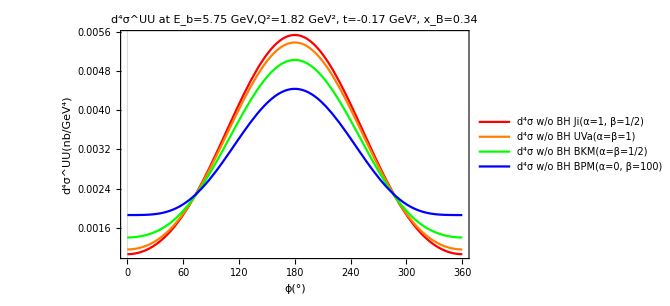

```mathematica
Plot[{
 CrossSection[0,0,0]/.ϕ->ϕp/180*π/.kinematicSetting1/.{αParameter->1,βParameter->1/2},
CrossSection[0,0,0]/.ϕ->ϕp/180*π/.kinematicSetting1/.{αParameter->1,βParameter->1}, CrossSection[0,0,0]/.ϕ->ϕp/180*π/.kinematicSetting1/.{αParameter->1/2,βParameter->1/2},
CrossSection[0,0,0]/.ϕ->ϕp/180*π/.kinematicSetting1/.{αParameter->0,βParameter->100}
},
{ϕp,0,360},
PlotLegends->Placed[
LineLegend[
{"d^4σ w/o BH Ji(α=1, β=1/2)",
"d^4σ w/o BH UVa(α=β=1)",
"d^4σ w/o BH BKM(α=β=1/2)",
"d^4σ w/o BH BPM(α=0, β=100)"},
LegendLayout->{"Row",4}
],
{0.25,0.8}],
FrameStyle->Black,
FrameLabel->{"ϕ(°)","d^4σ^UU(nb/GeV^4)"},
PlotStyle->{Red, Orange, Green, Blue},
PlotLabel->"d^4σ^UU at E_b=5.75 GeV,Q^2=1.82 GeV^2, t=-0.17 GeV^2, x_B=0.34",
PlotRange->All,
PlotTheme -> "Scientific"]
```

### (#X.3.1): d^4 σ w/o BH | (+) Polarized Beam | Unpolarized Target:

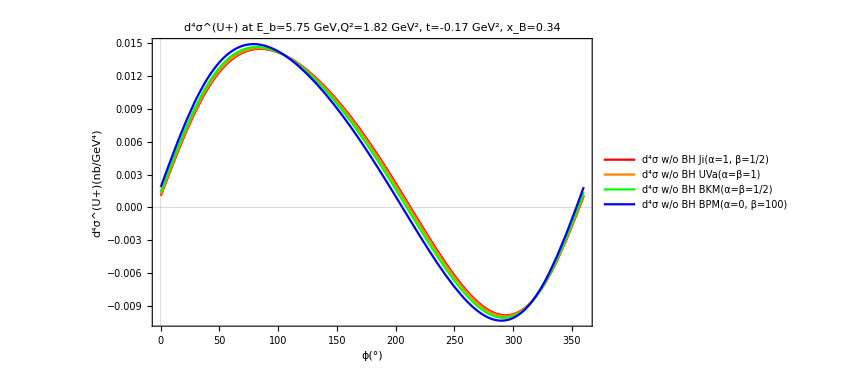

```mathematica
Plot[{
 CrossSection[1/2,0,0]/.ϕ->ϕp/180*π/.kinematicSetting1/.{αParameter->1,βParameter->1/2},
CrossSection[1/2,0,0]/.ϕ->ϕp/180*π/.kinematicSetting1/.{αParameter->1,βParameter->1}, CrossSection[1/2,0,0]/.ϕ->ϕp/180*π/.kinematicSetting1/.{αParameter->1/2,βParameter->1/2},
CrossSection[1/2,0,0]/.ϕ->ϕp/180*π/.kinematicSetting1/.{αParameter->0,βParameter->100}
},
{ϕp,0,360},
PlotLegends->Placed[
LineLegend[
{"d^4σ w/o BH Ji(α=1, β=1/2)",
"d^4σ w/o BH UVa(α=β=1)",
"d^4σ w/o BH BKM(α=β=1/2)",
"d^4σ w/o BH BPM(α=0, β=100)"},
LegendLayout->{"Row",4}
],
{0.25,0.78}],
FrameStyle->Black,
FrameLabel->{"ϕ(°)","d^4σ^(U+)(nb/GeV^4)"},
PlotStyle->{Red, Orange, Green, Blue},
PlotLabel->"d^4σ^(U+) at E_b=5.75 GeV,Q^2=1.82 GeV^2, t=-0.17 GeV^2, x_B=0.34",
PlotRange->All,
PlotTheme -> "Scientific"]
```

### (#X.3.1): d^4 σ w/o BH | (-) Polarized Beam | Unpolarized Target:

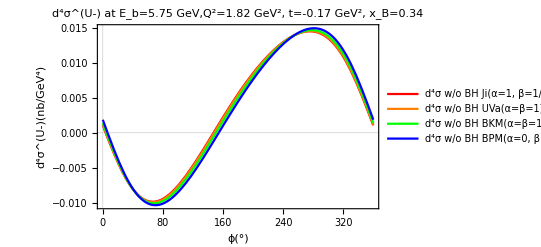

```mathematica
Plot[{
 CrossSection[-1/2,0,0]/.ϕ->ϕp/180*π/.kinematicSetting1/.{αParameter->1,βParameter->1/2},
CrossSection[-1/2,0,0]/.ϕ->ϕp/180*π/.kinematicSetting1/.{αParameter->1,βParameter->1}, CrossSection[-1/2,0,0]/.ϕ->ϕp/180*π/.kinematicSetting1/.{αParameter->1/2,βParameter->1/2},
CrossSection[-1/2,0,0]/.ϕ->ϕp/180*π/.kinematicSetting1/.{αParameter->0,βParameter->100}
},
{ϕp,0,360},
PlotLegends->Placed[
LineLegend[
{"d^4σ w/o BH Ji(α=1, β=1/2)",
"d^4σ w/o BH UVa(α=β=1)",
"d^4σ w/o BH BKM(α=β=1/2)",
"d^4σ w/o BH BPM(α=0, β=100)"},
LegendLayout->{"Row",4}
],
{0.25,0.78}],
FrameStyle->Black,
FrameLabel->{"ϕ(°)","d^4σ^(U-)(nb/GeV^4)"},
PlotStyle->{Red, Orange, Green, Blue},
PlotLabel->"d^4σ^(U-) at E_b=5.75 GeV,Q^2=1.82 GeV^2, t=-0.17 GeV^2, x_B=0.34",
PlotRange->All,
PlotTheme -> "Scientific"]
```

### (#X.3.1): d^4 σ w/o BH | Unpolarized Beam | Longitudinally-Polarized Target:

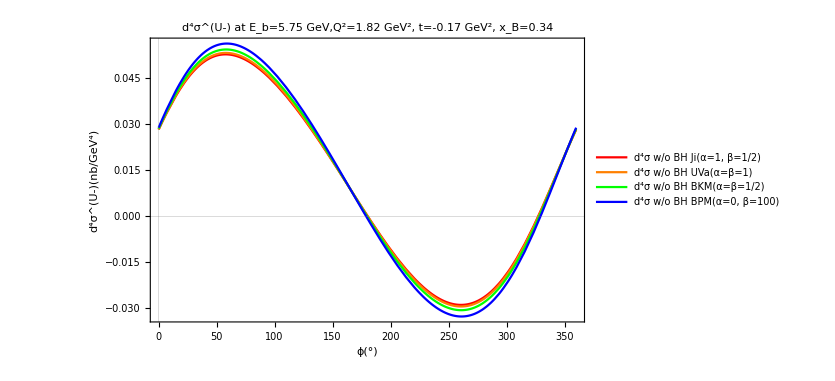

```mathematica
Plot[{
1/2( CrossSection[1/2,1,0]+ CrossSection[1/2,1,0])/.ϕ->ϕp/180*π/.kinematicSetting1/.{αParameter->1,βParameter->1/2},
1/2( CrossSection[1/2,1,0]+ CrossSection[1/2,1,0])/.ϕ->ϕp/180*π/.kinematicSetting1/.{αParameter->1,βParameter->1}, 1/2( CrossSection[1/2,1,0]+ CrossSection[1/2,1,0])/.ϕ->ϕp/180*π/.kinematicSetting1/.{αParameter->1/2,βParameter->1/2},
1/2( CrossSection[1/2,1,0]+ CrossSection[1/2,1,0])/.ϕ->ϕp/180*π/.kinematicSetting1/.{αParameter->0,βParameter->100}
},
{ϕp,0,360},
PlotLegends->Placed[
LineLegend[
{"d^4σ w/o BH Ji(α=1, β=1/2)",
"d^4σ w/o BH UVa(α=β=1)",
"d^4σ w/o BH BKM(α=β=1/2)",
"d^4σ w/o BH BPM(α=0, β=100)"},
LegendLayout->{"Row",4}
],
{0.25,0.78}],
FrameStyle->Black,
FrameLabel->{"ϕ(°)","d^4σ^(U-)(nb/GeV^4)"},
PlotStyle->{Red, Orange, Green, Blue},
PlotLabel->"d^4σ^(U-) at E_b=5.75 GeV,Q^2=1.82 GeV^2, t=-0.17 GeV^2, x_B=0.34",
PlotRange->All,
PlotTheme -> "Scientific"]
```

### (#X.3.1): d^4 σ w/o BH | (+) Polarized Beam | Longitudinally-Polarized Target:

### (#X.3.1): d^4 σ w/o BH | (-) Polarized Beam | Longitudinally-Polarized Target:

## (#X.4): Some Analysis Plots of d^4 σ w/o BH:

### (#X.4.1): d^4 σ w/o BH | All Cases:

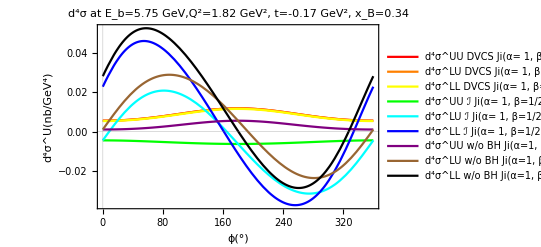

```mathematica
Plot[{
Γ*2π*389.9*1000*1/2( 𝒯DVCSSquared[1/2,0,0]+ 𝒯DVCSSquared[-1/2,0,0])/.ϕ->ϕp/180*π/.kinematicSetting1/.{αParameter->1,βParameter->1/2},
Γ*2π*389.9*1000* 1/2( 𝒯DVCSSquared[1/2,1,0]+ 𝒯DVCSSquared[-1/2,1,0])/.ϕ->ϕp/180*π/.kinematicSetting1/.{αParameter->1,βParameter->1/2},
Γ*2π*389.9*1000*  𝒯DVCSSquared[1/2,1,0]/.ϕ->ϕp/180*π/.kinematicSetting1/.{αParameter->1,βParameter->1/2},
Γ*2π*389.9*1000*1/2( ℐ[1/2,0,0]+ ℐ[-1/2,0,0])/.ϕ->ϕp/180*π/.kinematicSetting1/.{αParameter->1,βParameter->1/2},
Γ*2π*389.9*1000* 1/2( ℐ[1/2,1,0]+ ℐ[-1/2,1,0])/.ϕ->ϕp/180*π/.kinematicSetting1/.{αParameter->1,βParameter->1/2},
Γ*2π*389.9*1000*ℐ[1/2,1,0]/.ϕ->ϕp/180*π/.kinematicSetting1/.{αParameter->1,βParameter->1/2},
1/2( CrossSection[1/2,0,0]+ CrossSection[-1/2,0,0])/.ϕ->ϕp/180*π/.kinematicSetting1/.{αParameter->1,βParameter->1/2},
1/2( CrossSection[1/2,1,0]+ CrossSection[-1/2,1,0])/.ϕ->ϕp/180*π/.kinematicSetting1/.{αParameter->1,βParameter->1/2},
CrossSection[1/2,1,0]/.ϕ->ϕp/180*π/.kinematicSetting1/.{αParameter->1,βParameter->1/2}
},
{ϕp,0,360},
PlotLegends->Placed[
LineLegend[
{"d^4σ^UU DVCS Ji(α= 1, β=1/2)",
"d^4σ^LU DVCS Ji(α= 1, β=1/2)",
"d^4σ^LL DVCS Ji(α= 1, β=1/2)",
"d^4σ^UU ℐ Ji(α= 1, β=1/2)",
"d^4σ^LU ℐ Ji(α= 1, β=1/2)",
"d^4σ^LL ℐ Ji(α= 1, β=1/2)",
"d^4σ^UU w/o BH Ji(α=1, β=1/2)",
"d^4σ^LU w/o BH Ji(α=1, β=1/2)",
"d^4σ^LL w/o BH Ji(α=1, β=1/2)"},
LegendLayout->{"Row",7}
],
{0.25,0.25}],
FrameStyle->Black,
FrameLabel->{"ϕ(°)","d^4σ^U(nb/GeV^4)"},
PlotStyle->{
Red, Orange, Yellow, Green, Cyan, Blue, Purple, Brown, Black
},
PlotLabel->"d^4σ at E_b=5.75 GeV,Q^2=1.82 GeV^2, t=-0.17 GeV^2, x_B=0.34",
PlotRange->All,
PlotTheme -> "Scientific"]
```

## (#9): Sanity-Checks/Proofs

## (#X.1): Proving Our Twist-2 Unpolarized DVCS Code Matches Ji’s:

Here, we prove that our rewriting of Ji’s notebook and stuff is actually producing the same numbers!

### (#X.1.1): Ji/Yuxun’s Definitions:

#### (#X.1.1.1): F2UU | Ji’s Definitions:

```mathematica
F2UU=(1/M^2(4 M^2 (Imaginaryℋ^2+Realℋ^2)-(Imaginaryℰ^2+Realℰ^2) t-4 M^2 ((Imaginaryℰ+Imaginaryℋ)^2+(Realℰ+Realℋ)^2) ξ^2)+4 (ImaginaryℋT^2+RealℋT^2)-1/M^2(4 M^2 (2 ImaginaryℰT ImaginaryℋT+ImaginaryℋT^2+RealℋT (2 RealℰT+RealℋT))+(ImaginaryℰT^2+RealℰT^2) t) ξ^2)/4;
```

#### (#X.1.1.2): hampc | Ji’s Definitions:

```mathematica
hampc=Simplify[ScalarProductExpand[Contract[(Q^4*LDVCSunp/.{Momentum[kp]->Momentum[k]-Momentum[q]})*ComplexConjugate[𝒯1[α3,α1]]*𝒯1[α4,α2]*(-MT[α3,α4])]]];
```

### (#X.1.2): Comparisons:

#### (#X.1.2.1): Ji/Yuxun’s Code | Comparisons:

```mathematica
Γ*2π*389.9*1000*((4*hampc*F2UU)/Q^4)/.ξsub/.ϕ->ϕp/180*π/.kinematicSetting1/.{αParameter->1/2,βParameter->1/2}//FullSimplify
```

-2.97342×10^-6 (1. Imaginaryℰ^2+0.15111 ImaginaryℰT^2-6.25661 Imaginaryℰ Imaginaryℋ+82.3367 Imaginaryℋ^2-6.25661 ImaginaryℰT ImaginaryℋT+82.3367 ImaginaryℋT^2+1. Realℰ^2+0.15111 RealℰT^2-6.25661 Realℰ Realℋ+82.3367 Realℋ^2-6.25661 RealℰT RealℋT+82.3367 RealℋT^2) (-2.70863+1. Cos[(π ϕp)/180]-0.0530164 Cos[(π ϕp)/90])

#### (#X.1.2.2): Our Code | Comparisons:

```mathematica
Γ*2π*389.9*1000*𝒯DVCSSquared[1,0,0]/.ϕ->ϕp/180*π/.kinematicSetting1/.{αParameter->1/2,βParameter->1/2}//FullSimplify
```

0.00856647-0.00316266 Cos[(π ϕp)/180]+0.000167673 Cos[(π ϕp)/90]

## (#X.2): Proving Our Twist-2 Unpolarized Code Matches Ji’s:

### (#X.2.1): Ji/Yuxun’s Definitions:

### (#X.2.2): Comparisons:

#### (#X.2.2.1): Ji/Yuxun’s Code | Comparisons:

```mathematica
((Γ*2π*389.9*1000*1/(-Q^2 t)(AINTunpc(f1 Realℋ-t/(4M^2)f2 Realℰ)+BINTunpc(f1+f2)(Realℋ+Realℰ)+CINTunpc(f1+f2)RealℋT))/.ξsub)/.{f1->(GE-t/(4 M^2)GM)/(1-t/(4 M^2)),f2->(-GE+GM)/(1-t/(4 M^2))}/.ξsub/.ϕ->ϕp/180*π/.kinematicSetting1/.{αParameter->1/2,βParameter->1/2}//FullSimplify
```

(-0.00651288 Realℰ+0.0736802 Realℋ-0.0224903 RealℋT+(0.0118673 Realℰ+0.0634083 Realℋ+0.058347 RealℋT) Cos[(π ϕp)/180]+(-0.00197096 Realℰ-0.0168209 Realℋ-0.00984679 RealℋT) Cos[(π ϕp)/90]+(0.0000989229 Realℰ+0.0010246 Realℋ+0.000508962 RealℋT) Cos[(π ϕp)/60])/(19.9271-9.43104 Cos[(π ϕp)/180]+0.5 Cos[(π ϕp)/90])

#### (#X.2.2.2): Our Code | Comparisons:

```mathematica
FullSimplify[
Γ*2π*389.9*1000*ℐ[0,0,0]/.ϕ->ϕp/180*π/.kinematicSetting1/.{αParameter->1/2,βParameter->1/2}/.eL->1,
ϕp∈Reals]
```

(-0.117534+0.0793026 Cos[(π ϕp)/180]-0.00791087 Cos[(π ϕp)/90]+0.000271314 Cos[(π ϕp)/60])/(19.9271-9.43104 Cos[(π ϕp)/180]+0.5 Cos[(π ϕp)/90])

## (#X.3): Why does the Polarized Target case for the Interference Term break?

There seems to be unevaluated FeynCalc stuff going on that is causing the plotting thing to break.

### (#X.3.1): Checking the Unpolarized Beam/Unpolarized Target Interference Function:

#### (#X.3.1.1): Evaluating IFuu:

```mathematica
-1/(Q^2 t)IFuu/.ξsub/.ϕ->ϕp/180*π/.kinematicSetting1/.{αParameter->1,βParameter->1/2}//FullSimplify
```

3.23206 Re[((-253.615-338.437 ⅈ)+(156.219-497.265 ⅈ) Cos[(π ϕp)/180]-(14.1922-117.098 ⅈ) Cos[(π ϕp)/90]+(0.426946-6.89044 ⅈ) Cos[(π ϕp)/60])/(19.9271-9.43104 Cos[(π ϕp)/180]+0.5 Cos[(π ϕp)/90])]

#### (#X.3.1.2): Evaluating the Function ℐ:

```mathematica
ℐ[0,0,0]/.ϕ->ϕp/180*π/.kinematicSetting1/.{αParameter->1,βParameter->1/2}//FullSimplify
```

3.23206 Re[((-253.615-338.437 ⅈ)+(156.219-497.265 ⅈ) Cos[(π ϕp)/180]-(14.1922-117.098 ⅈ) Cos[(π ϕp)/90]+(0.426946-6.89044 ⅈ) Cos[(π ϕp)/60])/(19.9271-9.43104 Cos[(π ϕp)/180]+0.5 Cos[(π ϕp)/90])]

#### (#X.3.1.3): Proving IFuu and ℐ are the Same:

```mathematica
(ℐ[0,0,0]/.ϕ->ϕp/180*π/.kinematicSetting1/.{αParameter->1,βParameter->1/2})-(-1/(Q^2 t)IFuu/.ξsub/.ϕ->ϕp/180*π/.kinematicSetting1/.{αParameter->1,βParameter->1/2})
```

0.

### (#X.3.2): Checking the Unpolarized Beam/Polarized Target Interference Function:

This is the function that has problems. What we are going to do is do the same cross-check as above. Once that checks out (because there’s no way it won’t), we will have the confidence to say that the issue lies within the way that the FeynCalc thing has been coded.

#### (#X.3.2.1): Evaluating IFul:

```mathematica
-1/(Q^2 t)(IFuu+2*1* IFul)/.ξsub/.ϕ->ϕp/180*π/.kinematicSetting1/.{αParameter->1,βParameter->1/2}//FullSimplify
```

3.23206 (-2 Im[((487.487-576.045 ⅈ) Sin[(π ϕp)/180]-(87.9019-107.44 ⅈ) Sin[(π ϕp)/90]+(4.66025-5.69609 ⅈ) Sin[(π ϕp)/60])/(19.9271-9.43104 Cos[(π ϕp)/180]+0.5 Cos[(π ϕp)/90])]+Re[((-253.615-338.437 ⅈ)+(156.219-497.265 ⅈ) Cos[(π ϕp)/180]-(14.1922-117.098 ⅈ) Cos[(π ϕp)/90]+(0.426946-6.89044 ⅈ) Cos[(π ϕp)/60])/(19.9271-9.43104 Cos[(π ϕp)/180]+0.5 Cos[(π ϕp)/90])])

#### (#X.3.2.2): The Combination Above Should be the Same as the Explicit Function:

```mathematica
(-1/(Q^2 t)(IFuu+2*1* IFul)/.ξsub/.ϕ->ϕp/180*π/.kinematicSetting1/.{αParameter->1,βParameter->1/2}//FullSimplify)-(-1/(Q^2 t)(IFuu+2 1* IFul+2 0*(IFutIn Cos[ϕS-ϕ]+IFutOut Sin[ϕS-ϕ])+2 0(IFlu + 2 1 *IFll+2 0(IFltIn Cos[ϕS-ϕ]+IFltOut Sin[ϕS-ϕ])))/.ξsub/.ϕ->ϕp/180*π/.kinematicSetting1/.{αParameter->1,βParameter->1/2}//FullSimplify)//FullSimplify
```

0.

#### (#X.3.2.3): Evaluating the Function ℐ:

```mathematica
ℐ[0,1,0]/.ϕ->ϕp/180*π/.kinematicSetting1/.{αParameter->1/2,βParameter->1/2}//FullSimplify
```

3.23206 (-2 Im[((483.071-606.496 ⅈ) Sin[(π ϕp)/180]-(87.0195-113.193 ⅈ) Sin[(π ϕp)/90]+(4.61346-6.00107 ⅈ) Sin[(π ϕp)/60])/(19.9271-9.43104 Cos[(π ϕp)/180]+0.5 Cos[(π ϕp)/90])]+Re[((-263.975-330.294 ⅈ)+(178.11-517.058 ⅈ) Cos[(π ϕp)/180]-(17.7674-120.473 ⅈ) Cos[(π ϕp)/90]+(0.609359-7.0647 ⅈ) Cos[(π ϕp)/60])/(19.9271-9.43104 Cos[(π ϕp)/180]+0.5 Cos[(π ϕp)/90])])

#### (#X.3.2.4): Proving IFuu and ℐ are the Same:

```mathematica
(-1/(Q^2 t)(IFuu+2*1* IFul)/.ξsub/.ϕ->ϕp/180*π/.kinematicSetting1/.{αParameter->1/2,βParameter->1/2})-( ℐ[0,1,0]/.ϕ->ϕp/180*π/.kinematicSetting1/.{αParameter->1/2,βParameter->1/2})//FullSimplify
```

0.